```mathematica
α=7.297352533 10^-3;
H[x_,y_,β_]:=(α*β)/(2*π)*(1/(√(x*(1-x)))*ArcTan[√(x/(1-x))]-1+π(λ[y,β] x)/(1-x-λ[y,β]^2)) Exp[-(2y)/β];
H0[x_,y_,β_]:=(α*β)/(2*π)*(1/(√(x*(1-x)))*ArcTan[√(x/(1-x))]-1) Exp[-(2y)/β];
dH[x_,y_,β_]:=((x+(2 *x -1))/(2*x^2*(1-x)) √(x/(1-x))ArcTan[ √(x/(1-x))]+(π(1-λ[y,β])^2 λ[y,β])/((1-λ[y,β]^2-x)^2))Exp[-(2y)/β];
u1[y_,β_]:=(2 β^2)/(α^2 y^2)*Exp[ExpIntegralEi[-(2y)/β]];
λ[y_,β_]:= α/2 (Log[4.5 u1[y,β]]-2.44 Log[Log[0.15 u1[y,β]]]);
LDis1=Table[x/.FindRoot[x-y+H0[x,y,200],{x,0.9999,0.99999},MaxIterations->1000],{y,0,100,0.1}];
```

```mathematica
LDis2=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.99999},MaxIterations->1000],{y,0.0000000001,80,0.1}];
```

```mathematica
LDis22={0.08290201632109075,0.16385235233435635,0.242349990972648,0.317941419438368,0.39013185236360565,0.45838932792499343,0.5221698630223364,0.5809617618530176,0.6343456220230954,0.682058776639578,0.7240453758299448,0.7604731871233416,0.7917091081156463,0.8182619838908367,0.8407126440097589,0.8596508783194002,0.8756305642293666,0.8891447012044094,0.9006163616312193,0.9103999234513827,0.9187877205224687,0.9260187790028825,0.932287705731374,0.9377527788743424,0.9425428854167701,0.9467632668162161,0.9505001803875462,0.9538246359603222,0.9567953720660589,0.9594612200319731,0.9618629814391978,0.9640349213725574,0.9660059592485472,0.9678006217508954,0.9694398084281153,0.9709414094286001,0.9723208061706711,0.9735912789951952,0.9747643406094522,0.9758500100864763,0.9768570390288654,0.9777930990801174,0.978664938058738,0.9794785105138234,0.9802390873378239,0.9809513481599663,0.9816194595233456,0.9822471412776672,0.9828377231653342,0.9833941932156086,0.9839192392704322,0.9844152847310326,0.9848845194248715,0.9853289263386535,0.9857503048364407,0.9861502908900144,0.9865303747275193,0.9868919163111526,0.9872361589049261,0.987564241019849,0.9878772069463121,0.9881760160576543,0.988461551138662,0.9887346255207232,0.9889959898004288,0.9892463375392654,0.9894863104714077,0.9897165031434239,0.9899374670729502,0.9901497144827676,0.9903537216592567,0.9905499319780655,0.9907387586342165,0.9909205871094682,0.991095777405495,0.9912646660681055,0.9914275680246607,0.9915847782542409,0.9917365733078318,0.9918832126938121,0.9920249401422884,0.992161984760308,0.9922945620778275,0.9924228750677137,0.9925471149347249,0.992667462019527,0.9927840865112346,0.9928971491387949,0.9930068018063837,0.9931131881780854,0.9932164442176694,0.9933166986866032,0.993414073604878,0.9935086846772794,0.9936006416882285,0.9936900488678055,0.9937770052313539,0.9938616048948355,0.9939439373679122,0.9940240878265448,0.9941021373667444,0.9941781632409609,0.9942522390784659,0.9943244350983883,0.9943948182759524,0.9944634525560573,0.9945303990004568,0.9945957159493285,0.9946594591681713,0.9947216819854263,0.9947824354214891,0.9948417683074513,0.9948997274097521,0.9949563575157275,0.9950117015533376,0.995065800677682,0.9951186943594266,0.9951704204696513,0.9952210153579955,0.995270513926775,0.9953189497010573,0.9953663548943128,0.9954127604698515,0.9954581962055897,0.9955026907365127,0.9955462716207647,0.995588965381203,0.9956307975593639,0.995671792749158,0.9957119746491703,0.995751366098038,0.9957899891128901,0.9958278649253112,0.9958650140153427,0.9959014561438853,0.9959372103832845,0.995972295146521,0.9960067282122986,0.9960405267639445,0.9960737073905053,0.9961062861326696,0.9961382784960544,0.9961696994738523,0.9962005635675786,0.9962308848066977,0.9962606767673533,0.9962899525899631,0.9963187249966178,0.9963470063069231,0.9963748084536248,0.9964021429973701,0.9964290211408157,0.9964554537421111,0.9964814513277852,0.9965070241050661,0.9965321819736642,0.9965569345370435,0.9965812911132061,0.9966052607450194,0.9966288522100994,0.9966520740302797,0.9966749344806816,0.9966974415984078,0.9967196031908742,0.9967414268437993,0.9967629199288679,0.9967840896110817,0.9968049428558151,0.9968254864355844,0.9968457269360358,0.9968656707646865,0.9968853241521596,0.9969046931623202,0.9969237836954888,0.9969426014965039,0.9969611521547583,0.9969794411142123,0.996997473675542,0.9970152550014412,0.9970327901207117,0.9970500839326908,0.9970671412110341,0.9970839666081397,0.9971005646584031,0.9971169397820809,0.9971330962889124,0.9971490383810351,0.9971647701572044,0.997180295614438,0.9971956186524594,0.9972107430759027,0.9972256725972732,0.9972404108396602,0.997254961339349,0.9972693275483321,0.9972835128367177,0.9972975204970932,0.9973113537407964,0.99732501570746,0.9973385094629966,0.9973518380025598,0.9973650042525355,0.9973780110724669,0.9973908612569161,0.9974035575372635,0.9974161025834491,0.9974284990056548,0.997440749355931,0.9974528561297668,0.9974648217676044,0.997476648657577,0.9974883391328883,0.9974998954783698,0.9975113199288097,0.9975226146709262,0.997533781844629,0.9975448235442426,0.99755574181969,0.9975665386775486,0.9975772160825224,0.9975877759580049,0.9975982201874574,0.9976085506153456,0.9976187690481246,0.9976288772551947,0.9976388769698294,0.9976487698900759,0.9976585576796282,0.9976682419686765,0.99767782435473,0.9976873064034166,0.9976966896492608,0.9977059755964367,0.9977151657195016,0.997724261464108,0.9977332642476954,0.9977421754601622,0.9977509964645203,0.9977597285975287,0.9977683731703126,0.9977769314689626,0.9977854047551191,0.9977937942665399,0.9978103268000912,0.9978184721832195,0.9978265385146388,0.997834526920683,0.9978424385068997,0.9978502743585197,0.997858035540912,0.9978657231000286,0.9978733380628372,0.9978808814377413,0.9978883542149909,0.9978957573671721,0.9979030918491495,0.9979103585989318,0.9979175585391467,0.997924692573819,0.9979317615928831,0.9979387664699871,0.9979457080637167,0.9979525872177454,0.9979594047611382,0.9979661615086749,0.9979728582611448,0.99797949580563,0.9979860749157713,0.9979925963528411,0.9979990608636726,0.9980054691837645,0.9980118220359423,0.9980181201309581,0.9980243641677364,0.9980305548336164,0.9980366928045855,0.9980427787455112,0.9980488133103655,0.9980547971424486,0.9980607308746089,0.9980666151294695,0.998072450518836,0.9980782376463243,0.9980839771045458,0.9980896694770167,0.9980953153379666,0.9981009152525178,0.9981064697768629,0.9981119794584363,0.9981174448360808,0.9981228664402072,0.998128244792943,0.9981335804086366,0.9981388737930168,0.9981441254445342,0.9981493358538427,0.9981545055040866,0.9981596348710416,0.9981647244232514,0.9981797587712378,0.9981846936099651,0.9981895908728217,0.9981944509876927,0.9981992743761146,0.9982040614533911,0.9982088126287055,0.9982135283052314,0.9982182088802406,0.9982228547452093,0.9982274662859213,0.9982320438825697,0.9982365879098563,0.9982410987370877,0.998245576728272,0.9982500222422112,0.9982544356325923,0.9982588172480769,0.9982631674323885,0.9982674865243985,0.9982717748582103,0.9982760327632406,0.9982802605643011,0.9982844585816767,0.9982886271312033,0.998292766524343,0.998296877068259,0.9983009590658878,0.9983050128160106,0.9983090386133239,0.9983130367485069,0.9983170075082891,0.9983209511755079,0.9983248680292155,0.9983287583446565,0.9983326223934158,0.9983364604434367,0.9983402727590884,0.9983440596012253,0.9983478212272436,0.9983515578911385,0.9983552698435579,0.998358957331858,0.9983626206001553,0.9983662598893795,0.9983698754373237,0.9983734674786947,0.9983770362451632,0.9983805819654101,0.9983841048651759,0.9983876051673053,0.998391083091594,0.998394538855679,0.9983979726737352,0.9984013847574768,0.9984047753159423,0.9984081445555361,0.9984114926800691,0.998414819890799,0.9984181263864697,0.9984214123633488,0.9984246780152674,0.9984279235336554,0.998431149107579,0.9984343549237766,0.9984375411666939,0.9984407080185179,0.9984438556592118,0.9984469842665474,0.9984500940161394,0.9984531850814754,0.9984562576339494,0.9984593118428922,0.9984623478756014,0.9984653658973724,0.9984683660715272,0.9984713485594432,0.9984743135205822,0.998477261112518,0.9984801914909641,0.9984831048098005,0.9984860012211,0.9984888808750476,0.998491743920439,0.9984945905039129,0.9984974207705771,0.998500234863857,0.9985030329255189,0.9985058150956952,0.9985085815129076,0.9985113323140892,0.9985140676346085,0.9985167876082901,0.9985194923674375,0.9985221820428536,0.9985327924719248,0.9985354086396624,0.9985380104781344,0.9985405981082055,0.9985431716493661,0.9985457312199251,0.9985482769366604,0.9985508089152554,0.998553327270005,0.9985558321140185,0.9985583235591337,0.9985608017159824,0.998563266693986,0.9985657186013529,0.9985681575452663,0.9985705836315106,0.9985729969649,0.9985753976490795,0.9985777857865865,0.998580161478871,0.9985825248263428,0.9985848759280328,0.9985872148824769,0.9985895417867653,0.9985918567370692,0.9985941598285453,0.9985964511553423,0.9985987308105859,0.998600998886709,0.9986032554746792,0.9986055006648823,0.99860773454667,0.9986099572084716,0.9986121687377993,0.9986143692212481,0.9986165587445988,0.9986187373926331,0.9986209052493596,0.9986230623978903,0.9986252089205,0.9986273448986285,0.9986294704128905,0.998631585543086,0.9986336903682107,0.9986357849664661,0.9986378694152689,0.9986399437912593,0.9986420081703177,0.9986440626275633,0.9986461072373708,0.998648142073377,0.9986501672084906,0.998652182714901,0.9986541886640866,0.9986561851268235,0.998658172173195,0.9986601498725981,0.9986621182937537,0.9986640775047135,0.9986660275728683,0.9986679685649559,0.9986699005470694,0.9986718235846663,0.9986737377425756,0.9986756430849977,0.9986775396755213,0.9986794275771277,0.9986813068521975,0.9986831775626229,0.9986850397694105,0.9986868935332731,0.9986887389142594,0.9986905759718517,0.9986924047649732,0.9986942253519941,0.9986960377907373,0.9986978421384862,0.9986996384519896,0.9987014267874689,0.998703207200623,0.9987049797466353,0.9987067444801795,0.9987085014554246,0.9987102507260416,0.9987119923452085,0.9987137263656163,0.9987154528394744,0.9987171718185159,0.9987188833540032,0.9987205874967329,0.9987222842970415,0.9987239738048104,0.9987256560694705,0.9987273311400084,0.99872899906497,0.998730659892466,0.998732313670177,0.9987339604453545,0.9987356002648378,0.9987372331750417,0.9987388592219723,0.9987404784512277,0.9987420909080038,0.9987436966370977,0.9987452956829125,0.9987468880894617,0.9987484739003726,0.9987500531588916,0.9987516259079708,0.9987531921899645,0.998754752046999,0.9987563055209828,0.9987578526532312,0.9987593934847893,0.9987609280563474,0.9987624564082469,0.9987639785804824,0.998765494612706,0.9987670045442314,0.9987685084140365,0.9987700062607703,0.9987714981227455,0.9987729840379589,0.9987744640440828,0.9987759381784712,0.9987774064781636,0.9987788689798884,0.9987803257200655,0.9987817767348103,0.9987832220599361,0.9987846617309577,0.9987860957830946,0.9987875242512734,0.9987889471701314,0.9987903645740197,0.9987917764970051,0.9987931829728744,0.9987945840351362,0.9987959797170243,0.998797370051467,0.9987987550712394,0.9988001348087089,0.9988015092960407,0.9988028785651369,0.99880424264764,0.9988056015749358,0.9988069553781561,0.9988083040881818,0.9988096477356448,0.9988109863509317,0.9988202182588815,0.9988215176819318,0.9988228123356033,0.9988241022479506,0.9988253874468109,0.9988266679598011,0.9988279438143217,0.998829215037559,0.9988304816564866,0.9988317436978685,0.9988330011882297,0.9988342541540053,0.9988355026212691,0.9988367466159774,0.9988379861638772,0.9988392212905142,0.9988404520212372,0.9988416783812005,0.9988429003953312,0.9988441180884948,0.9988453314851948,0.9988465406098347,0.998847745486632,0.9988489461396121,0.9988501425926178,0.9988513348693125,0.99885252299314,0.9988537069875242,0.9988548868754901,0.9988560626800236,0.9988572344239148,0.9988584021297805,0.9988595658200582,0.9988607255170574,0.998861881242863,0.9988630330194354,0.9988641808685619,0.998865324811869,0.998866464870819,0.9988687334207516,0.9988698619538733,0.9988709866869415,0.99887210764063,0.9988732248355262,0.99887433829197,0.9988754480302187,0.9988765540703658,0.9988776564323375,0.9988787551360028,0.9988798502009546,0.9988809416467352,0.9988820294927206,0.9988831137581535,0.9988841944621116,0.9988852716236148,0.9988863452614364,0.9988874153942959,0.9988884820407332,0.9988895452191922,0.9988906049479687,0.9988916612452295,0.9988927141290136,0.9988937636172324,0.9988948097276713,0.9988958524779904,0.9988968918857191,0.9988979279682898,0.9988989607429749,0.9988999902269496,0.9989010164372654,0.998902039390853,0.998903059104525,0.9989040755949817,0.9989050888788011,0.9989060989724534,0.9989071058922823,0.9989081096545367,0.9989091102753412,0.9989101077707073,0.998911102156561,0.9989120934486811,0.9989130816627643,0.998914066814388,0.9989150489190426,0.9989160279920939,0.9989170040488025,0.9989179771043363,0.9989189471737561,0.998919914272021,0.9989208784139889,0.9989218396144179,0.9989227978879668,0.9989237532491955,0.9989247057125666,0.998925655292445,0.9989266020030971,0.99892754585872,0.9989284868733662,0.9989294250610325,0.9989303604355994,0.9989312930109092,0.9989322228006327,0.9989331498184018,,0.9989368304392121,0.9989377437983932,0.9989386544654795,0.9989395624534773,0.998940467775308,0.9989413704437987,0.9989422704717179,0.998943167871728,0.998944062656464,0.9989449548383615,0.9989458444298571,0.9989467314433702,0.9989476158910976,0.9989484977852352,0.9989493771379119,0.9989502539611547,0.9989511282669181,0.9989520000670854,0.9989528693734459,0.998953736197761,0.9989546005516532,0.9989554624467132,0.9989563218944478,0.9989571789062921,0.9989580334936274,0.9989588856676774,0.99895973543973,0.9989605828209104,0.9989614278222958,0.9989622704548903,0.9989631107296568,0.9989639486574418,0.9989647842490582,0.9989656175152427,0.9989664484666654,0.9989672771139301,0.9989681034675747,0.9989689275380718,0.9989697493358293,0.9989705688711906,0.9989713861544348,0.9989722011957766,0.9989730140053961,0.9989738245933492,0.9989746329696801,0.9989754391443576,0.9989762431272897,0.9989770449283238,0.9989778445572475,0.9989786420237889,0.9989794373376172,0.9989802305083428,0.9989810215455086,0.9989818104586373,0.9989825972571388,0.9989833819504025,0.9989841645477527,0.9989849450584577,0.9989857234917301,0.9989864998567274,0.9989872741625521,0.9989880464182523,0.9989888166328216,0.9989895848151982,0.9989903509742917,0.9989911151189094,0.9989918772578446,0.9989926373998282,0.9989933955535396,0.9989941517276069,0.9989949059306072,0.9989956581710643,0.9989964084574511,0.9989971567982266,0.99899790320173,0.998998647676304,0.9989993902302289,0.9990001308717366,0.9990008696090109,0.9990016064501874,0.9990023414033522,0.9990030744765498,0.9990038056778032,0.9990045350150207,0.9990052624961229,0.9990059881289677,0.9990067119213684,0.9990074338810931,0.9990081540158655,0.9990088723333652,0.9990095888412273,0.9990103035470441,0.9990110164583622,0.9990117275826886,0.9990124369274924,0.9990131445001844,0.999014554358716,0.9990152566591776,0.9990159572168201,0.9990166560388193,0.9990173531323606,0.9990180485045764,0.9990187421625589,0.9990194341133602,0.9990201243639933,0.9990208129214323,0.9990214997926116,0.9990221849844101,0.9990228685037245,0.9990296131908052,0.9990302787544469,0.9990309427249768,0.9990316051087769,0.9990322659121945,0.9990329251415424,0.9990335828030993,0.9990342389031093,0.9990348934477827,0.9990355464432964,0.999036197895782,0.9990368478113829,0.9990374961961457,0.9990381430561223,0.9990387883973256,0.999039432225735,0.9990400745473034};
```

```mathematica
LDis3=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.999},MaxIterations->1000],{y,80,160,0.1}];
```

```mathematica
LDis32={0.9990407153679286,0.999041354693513,0.9990419925299024,0.9990426288829178,0.9990432637583491,0.9990438971619554,0.9990445290994653,0.9990451595765767,0.9990457885989572,0.9990464161722449,0.9990470423020471,0.9990476669939613,0.9990482902535042,0.9990489120862099,0.9990495324975691,0.9990501514930435,0.9990507690780663,0.9990513852580424,0.9990520000383478,0.9990526134243312,0.9990532254213128,0.9990538360345853,0.9990544452694138,0.9990550531310358,0.9990556596246623,0.9990562647554764,0.999056868528635,0.9990574709492679,0.9990580720224786,0.9990586717533446,0.9990592701469168,0.9990598672082199,0.9990604629422535,0.9990610573539911,0.9990616504483807,0.999062242230345,0.9990628327047818,0.9990634218765637,0.9990640097505384,0.999064596331529,0.9990651816243342,0.9990657656337282,0.9990663483644611,0.9990669298212588,0.9990675100088235,0.9990680889318341,0.9990686665949451,0.9990692430027691,0.9990698181599454,0.9990703920710452,0.9990709647406301,0.999071536173239,0.9990721063733878,0.9990726753455704,0.9990732430942579,0.9990738096238991,0.9990743749389207,0.999074939043725,0.9990755019426991,0.999076063640202,0.9990766241405732,0.9990771834481306,0.9990777415671707,0.999078298501969,0.9990788542567858,0.9990794088358433,0.9990799622433594,0.9990805144835258,0.9990810655605137,0.9990816154784744,0.9990821642415382,0.9990827118538154,0.9990832583193964,0.9990838036423516,0.9990843478267315,0.999084890876567,0.9990854327958695,0.9990859735886306,0.9990865132588229,0.9990870518103997,0.9990875892472952,0.9990881255734245,0.999088660792684,0.9990891949089513,0.9990897279260852,0.9990902598479261,0.9990907906782959,0.9990913204209985,0.9990918490798192,0.9990923766585252,0.9990929031608662,0.9990934285905736,0.999093952951361,0.9990944762469249,0.9990949984809434,0.9990955196570778,0.9990960397789717,0.9990965588502518,0.9990970768745274,0.9990975938553908,0.9990981097964173,0.9990986247011657,0.9990991385731777,0.9990996514159782,0.9991001632330764,0.9991006740279641,0.9991011838041173,0.9991016925649956,0.9991022003140424,0.9991027070546853,0.9991032127903354,0.9991037175243886,0.9991042212602245,0.9991047240012072,0.9991052257506854,0.9991057265119918,0.9991062262884443,0.999106725083345,0.9991072228999811,0.9991077197416242,0.9991082156115314,0.9991087105129445,0.9991092044490906,0.9991096974231816,0.9991101894384151,0.999110680497974,0.9991111706050266,0.9991116597627268,0.9991121479742139,0.9991126352426133,0.9991131215710356,0.9991136069625779,0.9991140914203229,0.9991145749473395,0.9991150575466825,0.9991155392213931,0.9991160199744985,0.9991164998090125,0.9991169787279354,0.9991174567342536,0.9991179338309405,0.9991184100209558,0.9991188853072462,0.9991193596927451,0.9991198331803728,0.9991203057730363,0.9991207774736302,0.9991212482850356,0.9991217182101211,0.9991221872517425,0.9991226554127427,0.9991231226959524,0.9991235891041893,0.9991240546402589,0.9991245193069543,0.9991249831070561,0.9991254460433328,0.9991259081185405,0.9991263693354234,0.9991268296967135,0.9991272892051308,0.9991277478633834,0.9991282056741676,0.9991286626401678,0.9991291187640566,0.999129574048495,0.9991300284961326,0.9991304821096073,0.9991309348915453,0.9991313868445615,0.9991318379712598,0.9991322882742324,0.9991327377560604,0.9991331864193137,0.9991336342665512,0.9991340813003207,0.999134972937598,0.999135417546139,0.999135861351294,0.9991363043555563,0.999136746561409,0.9991371879713238,0.9991376285877623,0.9991380684131757,0.9991385074500042,0.999138945700678,0.999139383167617,0.9991398198532306,0.9991402557599182,0.9991406908900684,0.9991411252460607,0.9991415588302637,0.9991419916450361,0.999142423692727,0.9991428549756752,0.9991432854962099,0.9991437152566501,0.9991441442593058,0.9991445725064764,0.9991450000004523,0.9991454267435137,0.999145852737932,0.9991462779859684,0.9991467024898701,0.9991471262518927,0.99914754927426,0.9991479715591964,0.9991483931089176,0.9991488139256288,0.9991492340115269,0.9991496533687989,0.9991500719996183,0.9991504899061686,0.9991509070905956,0.9991513235550612,0.9991517393016907,0.9991521543326346,0.9991525686500121,0.9991529822559391,0.9991533951525228,0.9991538073418612,0.9991542188260434,0.9991546296071618,0.9991550396872753,0.9991554490684535,0.9991558577527532,0.9991562657422215,0.9991566730388982,0.9991570796448144,0.9991574855619928,0.9991578907924481,0.999158295338187,0.9991586992012075,0.9991591023834999,0.9991595048870464,0.9991599067138209,0.9991603078657895,0.9991607083449173,0.9991611081531446,0.9991615072924181,0.9991619057646728,0.9991623035718353,0.9991627007158256,0.9991630971985548,0.9991634930219272,0.9991638881878391,0.9991642826981794,0.9991646765548291,0.9991650697596625,0.9991654623145455,0.9991658542213374,0.9991662454818897,0.9991666360980465,0.9991670260716449,0.9991674154045145,0.999167804098478,0.999168192155351,0.999168579576942,0.9991689663650404,0.9991693525214573,0.9991697380479726,0.9991701229463659,0.9991705072184099,0.9991708908658707,0.9991712738905069,0.9991716562940707,0.9991720380783072,0.9991724192449548,0.9991727997957451,0.999173179732403,0.9991735590566466,0.9991739377701873,0.9991743158747294,0.9991746933719707,0.9991750702636071,0.9991754465513184,0.9991758222367848,0.9991761973216788,0.9991765718076657,0.9991769456964047,0.9991773189895479,0.9991776916887387,0.9991780637956311,0.9991784353118432,0.9991788062390082,0.9991791765787441,0.9991795463326736,0.9991799155024006,0.9991802840895283,0.9991806520956532,0.999181019522366,0.9991813863712514,0.9991817526438878,0.9991821183418477,0.9991824834666974,0.9991828480199977,0.9991832120033033,0.9991835754181627,0.9991839382661191,0.9991843005487092,0.9991846622674646,0.9991850234239106,0.9991853840195671,0.999185744055948,0.9991861035345617,0.9991864624569067,0.9991868208244902,0.9991871786387967,0.9991875359013125,0.999187892613518,0.9991882487768883,0.9991886043928924,0.9991889594629942,0.9991893139886521,0.9991896679713189,0.9991900214124422,0.9991903743134639,0.999190726675821,0.9991910785009448,0.9991914297902614,0.9991917805451918,0.9991921307671513,0.9991924804575546,0.9991928296177964,0.999193178249284,0.9991935263534121,0.9991938739315696,0.9991942209851412,0.9991945675155063,0.9991949135240392,0.9991952590121096,0.9991956039810816,0.9991966357869752,0.9991969786931005,0.9991973210868736,0.9991976629696309,0.9991980043427021,0.9991983452074126,0.999198685565083,0.9991990254170281,0.9991993647645594,0.9991997036089826,0.9992000419515988,0.999200379793704,0.9992007171365941,0.9992010539815516,0.9992013903298609,0.9992017261828,0.9992020615416426,0.9992023964076572,0.9992027307821084,0.9992030646662559,0.9992033980613549,0.9992037309686567,0.9992040633894074,0.9992043953248491,0.9992047267762197,0.9992050577447462,0.9992053882316659,0.9992057182381998,0.9992060477655677,0.9992063768149851,0.9992067053876638,0.9992070334848102,0.9992073611076273,0.9992076882573138,0.9992080149350636,0.9992083411420669,0.9992086668795096,0.9992089921485735,0.9992093169504358,0.9992096412862701,0.9992099651572454,0.9992102885645268,0.9992106115092754,0.9992109339926478,0.9992112560158031,0.9992115775798808,0.99921189868603,0.9992122193353914,0.9992125395291019,0.9992128592682948,0.9992131785540989,0.9992134973876393,0.9992138157700373,0.9992141337024103,0.9992144511858718,0.9992147682215312,0.9992150848104945,0.9992154009538586,0.9992157166527329,0.9992160319082051,0.9992163467213657,0.9992166610933019,0.9992169750250967,0.9992172885178294,0.999217601572576,0.9992179141904082,0.9992182263723944,0.9992185381195996,0.9992188494330843,0.9992191603139061,0.9992194707631189,0.9992197807817726,0.9992200903709141,0.9992203995315863,0.9992207082648284,0.999221016571677,0.9992213244531639,0.9992216319103184,0.9992219389441659,0.9992222455557283,0.999222551746024,0.9992228575160683,0.9992231628668727,0.9992234677994456,0.9992237723147918,0.9992240764139124,0.9992243800978059,0.9992246833674668,0.9992249862238869,0.9992252886680536,0.9992255907009522,0.9992258923235637,0.9992261935368666,0.9992264943418359,0.9992267947394429,0.9992270947306561,0.9992273943164407,0.9992276934977586,0.9992279922755689,0.9992282906508267,0.9992285886244847,0.999228886197492,0.9992291833707911,0.999229480145333,0.9992297765220529,0.9992300725018876,0.9992303680857706,0.9992306632746327,0.9992309580694012,0.9992312524710008,0.9992315464803528,0.9992318400983752,0.9992321333259836,0.9992324261640904,0.9992327186136049,0.9992330106754334,0.9992333023504794,0.9992335936396431,0.9992338845438223,0.9992341750639113,0.999234465200802,0.9992347549553828,0.9992350443285397,0.9992353333211558,0.9992356219341108,0.9992359101682824,0.9992361980245446,0.9992364855037691,0.9992367726068246,0.999237059334577,0.9992373456878892,0.999237631667622,0.9992379172746326,0.999238202509772,0.9992384873739014,0.9992387718678643,0.999239055992507,0.9992393397486738,0.9992396231372059,0.9992399061589418,0.9992401888147171,0.9992404711053651,0.9992407530317159,0.9992410345945976,0.999241315794835,0.9992415966332506,0.9992418771106644,0.9992421572278934,0.9992424369857524,0.9992427163850532,0.9992429954266056,0.999243274111216,0.9992435524396891,0.9992438304128245,0.9992441080314266,0.9992443852962883,0.9992446622082044,0.9992449387679666,0.9992452149763638,0.9992454908341829,0.9992457663422083,0.9992460415012215,0.999246316312002,0.9992465907753264,0.9992468648919695,0.9992471386627028,0.999247412088296,0.9992476851695135,0.9992479579071274,0.9992482303018946,0.9992485023545752,0.9992487740659275,0.9992490454367066,0.9992493164676655,0.9992495871595547,0.9992498575131226,0.9992501275291149,0.999250397208275,0.9992506665513445,0.9992509355590622,0.9992512042321647,0.9992514725713865,0.9992517405774596,0.9992520082511139,0.999252275593077,0.9992525426040745,0.9992528092848291,0.999253075636062,0.9992533416584917,0.9992536073528349,0.9992538727198056,0.999254137760116,0.9992544024744761,0.9992546668635935,0.9992549309281739,0.9992551946689204,0.9992554580865346,0.9992557211817155,0.99925598395516,0.9992562464075629,0.9992565085396172,0.9992567703520132,0.9992570318454433,0.9992572930205846,0.9992575538781283,0.999257814418756,0.9992580746431476,0.9992583345519813,0.999258594145933,0.9992588534256767,0.9992591123918845,0.9992593710452263,0.999259629386367,0.9992598874159815,0.9992601451347259,0.9992604025432638,0.9992606596422556,0.9992609164323591,0.9992611729142312,0.9992624507229328,0.9992627053690794,0.9992629597115315,0.9992632137509294,0.9992634674879121,0.999263720923116,0.999263974057176,0.9992642268907252,0.9992644794243944,0.9992647316588129,0.999264983594608,0.999265235232405,0.9992654865728278,0.999265737616498,0.9992659883640352,0.9992662388160611,0.9992664889731842,0.9992667388360238,0.9992669884051928,0.9992672376813015,0.9992674866649591,0.9992677353567726,0.9992679837573476,0.9992682318672877,0.9992684796871949,0.9992687272176694,0.9992689744593068,0.9992692214127117,0.9992694680784691,0.9992697144571816,0.9992699605494336,0.9992702063558174,0.9992704518769205,0.9992706971133303,0.9992709420656303,0.9992711867344038,0.9992714311202318,0.999271675223695,0.9992719190453699,0.9992721625858332,0.9992724058456594,0.9992726488254214,0.999272891525691,0.9992731339470355,0.9992733760900255,0.9992736179552262,0.9992738595432022,0.9992741008545168,0.9992743418897311,0.9992745826494049,0.9992748231340958,0.9992750633443638,0.9992753032807596,0.9992755429438385,0.999275782334152,0.9992760214522506,0.9992762602986829,0.9992764988739959,0.9992767371787352,0.9992769752134452,0.9992772129786679,0.9992774504749443,0.9992776877028128,0.9992779246628133,0.999278161355481,0.9992783977813509,0.999278633940956,0.9992788698348285,0.9992791054634983,0.9992793408274943,0.9992795759273477,0.9992798107635772,0.9992800453367103,0.9992802796472701,0.9992805136957778,0.9992807474827531,0.9992809810087149,0.9992812142741797,0.9992814472796634,0.9992816800256799,0.999281912512742,0.9992821447413608,0.9992823767120462,0.9992826084253065,0.9992828398816486,0.9992830710815781,0.9992833020255991,0.9992835327142142,0.999283763147925,0.9992839933272311,0.9992842232526312,0.9992844529246224,0.9992846823437006,0.9992849115103601,0.9992851404250939,0.9992853690883935,0.9992855975007496,0.9992858256626508,0.9992860535745848,0.9992862812370379,0.999286508650495,0.9992867358154395,0.999286962732354,0.9992871894017189,0.9992874158240143,0.9992876419997181,0.9992878679293075,0.999288093613258,0.9992883190520429,0.9992885442461369,0.9992887691960111,0.9992889939021357,0.9992892183649847,0.9992894425850181,0.999289666562706,0.9992898902985137,0.9992901137929053,0.9992903370463436,0.9992905600592902,0.9992907828322054,0.999291005365548,0.9992912276597763,0.9992914497153464,0.9992916715327139,0.9992918931123329,0.999292114454656,0.9992923355601352,0.9992925564292207,0.9992927770623617,0.9992929974600063,0.9992932176226011,0.9992934375505921,0.9992936572444232,0.9992938767045378,0.9992940959313779,0.9992943149253842,0.9992945336869966,0.9992947522166532,0.9992949705147913,0.9992951885818471,0.9992954064182553,0.9992956240244497,0.9992958414008677,0.9992960585479329,0.9992962754660789,0.999296492155735,0.9992967086173291,0.9992969248512882,0.9992971408580381,0.9992973566380032,0.9992975721916072,0.9992977875192723,0.9992980026214199,0.99929821749847,0.9992984321508416,0.9992986465789527,0.9992988607832203,0.9992990747640597,0.9992992885218852,0.9992995020571109,0.9992997153701488,0.9992999284614099,0.9993001413313097,0.9993003539802497,0.9993005664086412,0.999300778616891,0.9993009906054053,0.9993012023745887,0.9993014139248454,0.999301625256578,0.9993018363701882,0.9993020472660767,0.9993022579446432,0.9993024684062861,0.9993026786514031,0.9993028886803906,0.9993030984936442,0.999303308091558,0.9993035174745256,0.9993037266429395,0.9993039355971909,0.9993041443376741,0.9993043528647719,0.9993045611788753,0.999304769280372,0.9993049771696482,0.9993051848470891,0.9993053923130791,0.9993055995680016,0.999305806612239,0.9993060134461725,0.9993062200701828,0.9993064264846491,0.9993066326899497,0.9993068386864624,0.9993070444745634,0.9993072500546284,0.9993074554270319,0.9993076605921477,0.9993078655503482,0.9993080703020051,0.9993082748474891,0.9993084791871701,0.9993086833214171,0.9993088872505976,0.9993090909750789,0.9993092944952269,0.9993094978114063,0.9993097009239851,0.9993099038333209,0.9993101065397783,0.9993103090437188,0.9993105113455027,0.9993107134454899,0.999310915344039,0.9993111170415075,0.9993113185382526,0.99931151983463,0.9993117209309947,0.9993119218277011,0.9993121225251024,0.9993123230235508,0.999312523323398,0.9993127234249944,0.99931292332869,0.9993131230348333,0.9993133225437725,0.9993135218558545,0.9993137209714259,0.9993139198908316,0.9993141186144163,0.9993143171425235,0.9993145154754962,0.9993147136136761,0.9993149115574043,0.999315109307021,0.9993153068628657,0.9993155042252767,0.9993157013945918,0.9993158983711478,0.9993160951552805,0.9993162917473253,0.9993164881476165};
```

```mathematica
LDis42={0.9993164881476165,0.9993166843564876,0.9993168803742709,0.9993170762012987,0.999317271837902,0.9993174672844106,0.9993176625411543,0.9993178576084613,0.9993180524866596,0.9993182471760761,0.999318441677037,0.9993186359898676,0.9993188301148923,0.999319024052435,0.9993192178028166,0.9993194113663645,0.9993196047433959,0.9993197979342319,0.9993199909391927,0.9993201837585971,0.9993203763927635,0.9993205688420091,0.999320761106651,0.9993209531870048,0.9993211450833855,0.9993213367961103,0.9993215283254858,0.9993217196718301,0.9993219108354549,0.9993221018166707,0.9993222926157883,0.9993224832331175,0.9993226736689671,0.9993228639236456,0.9993230539974591,0.9993232438907179,0.9993234336037251,0.9993236231367866,0.9993238124902072,0.9993240016642893,0.9993241906593398,0.9993243794756573,0.9993245681135445,0.9993260708291214,0.9993262578745932,0.9993264447446123,0.9993266314394728,0.9993268179594618,0.99932700430488,0.9993271904760156,0.9993273764731597,0.9993275622966026,0.9993277479466338,0.9993279334235423,0.9993281187276163,0.9993283038591432,0.9993284888184097,0.9993286736057022,0.9993288582213061,0.9993290426655062,0.9993292269385864,0.99932941104083,0.9993295949725199,0.999329778733938,0.999329962325371,0.9993301457470912,0.9993303289993825,0.9993305120825242,0.9993306949967949,0.9993308777424732,0.9993310603198362,0.999331242729161,0.9993314249707234,0.9993316070447991,0.999331788951663,0.9993319706915893,0.9993321522648518,0.999332333671723,0.9993325149124757,0.9993326959873813,0.9993328768967109,0.999333057640735,0.9993332382197231,0.9993334186339445,0.9993335988836677,0.9993337789691606,0.9993339588906907,0.999334138648524,0.9993343182429272,0.9993344976741654,0.9993346769425032,0.9993348560482053,0.9993350349915324,0.9993352137727534,0.9993353923921267,0.9993355708499143,0.9993357491463775,0.9993359272817769,0.9993361052563723,0.999336283070423,0.9993364607241877,0.999336638217925,0.9993368155518918,0.9993369927263455,0.9993371697415421,0.9993373465977377,0.9993375232951872,0.9993376998341453,0.9993378762148659,0.9993380524376025,0.9993382285026079,0.9993384044101343,0.9993385801604336,0.9993387557537565,0.9993389311903539,0.9993391064704726,0.9993392815943687,0.9993394565622871,0.999339631374476,0.9993398060311833,0.9993399805326558,0.9993401548791405,0.9993403290708832,0.9993405031081294,0.9993406769911238,0.999340850720111,0.9993410242953346,0.9993411977170377,0.9993413709854632,0.9993415441008531,0.999341717063449,0.9993418898734918,0.9993420625312222,0.9993422350368799,0.9993424073907043,0.9993425795929345,0.9993427516438086,0.9993429235435642,0.9993430952924389,0.9993432668906692,0.9993434383384914,0.9993436096361409,0.999343780783853,0.9993439517818622,0.9993442933297079,0.9993444638800107,0.9993446342815437,0.999344804534539,0.999344974639228,0.9993451445958416,0.99934531440461,0.9993454840657634,0.9993456535795311,0.9993458229461418,0.9993459921658242,0.9993461612388059,0.9993463301653143,0.9993464989455764,0.9993466675798183,0.999346836068266,0.9993470044111448,0.9993471726086794,0.9993473406610945,0.9993475085686138,0.9993476763314605,0.9993478439498575,0.9993480114240304,0.9993481787541937,0.9993483459405732,0.9993485129833901,0.9993486798828642,0.9993488466392157,0.999349013252664,0.999349179723428,0.999349346051726,0.999349512237776,0.9993496782817958,0.9993498441840022,0.9993500099446118,0.9993501755638405,0.9993503410419043,0.9993505063790183,0.9993506715753968,0.9993508366312543,0.9993510015468046,0.9993511663222608,0.9993513309578357,0.9993514954537416,0.9993516598101907,0.999351824027394,0.9993519881055627,0.9993521520449073,0.9993523158456378,0.9993524795079636,0.9993526430320943,0.999352806418238,0.9993529696666033,0.9993531327773978,0.999353295750829,0.9993534585871002,0.9993536212864252,0.9993537838490062,0.9993539462750483,0.999354108564757,0.9993542707183369,0.999354432735992,0.9993545946179264,0.9993547563643432,0.9993549179754453,0.9993550794514352,0.999355240792515,0.9993554019988863,0.9993555630707498,0.9993557240083066,0.9993558848117572,0.999356045481301,0.9993562060171381,0.9993563664194667,0.999356526688486,0.9993566868243938,0.9993568468273881,0.9993570066976664,0.9993571664354248,0.9993573260408605,0.9993574855141688,0.9993576448555469,0.9993578040651885,0.9993579631432885,0.9993581220900425,0.9993582809056432,0.9993584395902843,0.9993585981441601,0.999358756567462,0.9993589148603831,0.999359073023115,0.9993592310558493,0.9993593889587772,0.9993595467320895,0.9993597043759763,0.9993598618906276,0.9993600192762329,0.9993601765329815,0.9993603336610617,0.9993604906606622,0.9993606475319707,0.999360804275175,0.999360960890462,0.9993611173780184,0.9993612737380306,0.9993614299706848,0.9993615860761662,0.9993617420546601,0.9993618979063513,0.9993620536314243,0.999362209230063,0.9993623647024511,0.9993625200487718,0.9993626752692081,0.9993628303639422,0.9993629853331565,0.9993631401770324,0.9993632948957517,0.999363449489495,0.999363603958443,0.9993637583027759,0.9993639125226736,0.9993640666183157,0.999364220589881,0.9993643744375483,0.999364528161496,0.9993646817619023,0.9993648352389446,0.9993649885928,0.9993651418236456,0.9993652949316579,0.9993654479170131,0.9993656007798869,0.9993657535204546,0.9993659061388915,0.9993660586353723,0.9993662110100712,0.9993663632631623,0.9993665153948191,0.999366667405215,0.9993668192945229,0.9993669710629153,0.9993671227105644,0.9993672742376422,0.99936742564432,0.999367576930769,0.9993689331265867,0.9993690832200851,0.9993692331952145,0.999369383052142,0.9993695327910341,0.9993696824120538,0.9993698319153745,0.9993699813011577,0.9993701305695689,0.999370279720773,0.9993704287549348,0.9993705776722183,0.9993707264727877,0.9993708751568069,0.9993710237244388,0.9993711721758466,0.999371320511193,0.9993714687306403,0.9993716168343506,0.9993717648224854,0.9993719126952062,0.999372060452674,0.9993722080950495,0.9993723556224932,0.999372503035165,0.9993726503332248,0.9993727975168318,0.9993729445861453,0.9993730915413243,0.9993732383825267,0.999373385109911,0.9993735317236352,0.9993736782238565,0.9993738246107309,0.9993739708844176,0.9993741170450718,0.9993742630928502,0.9993744090279126,0.9993745548504077,0.9993747005604938,0.9993748461583262,0.9993749916440571,0.9993751370178475,0.9993752822798454,0.9993754274302064,0.9993755724690839,0.9993757173966313,0.9993758622130015,0.999376006918347,0.99937615151282,0.9993762959965721,0.9993764403697566,0.9993765846325233,0.9993767287850235,0.9993768728274084,0.9993770167598282,0.99937716058243,0.9993773042953725,0.9993774478987978,0.9993775913928566,0.9993777347776983,0.9993778780534717,0.9993780212203253,0.9993781642784058,0.9993783072278647,0.9993784500688465,0.999378592801499,0.9993787354259694,0.9993788779424045,0.9993790203509499,0.9993791626517536,0.9993793048449606,0.9993794469307143,0.9993795889091626,0.9993797307804488,0.9993798725447203,0.9993800142021186,0.9993801557527889,0.9993802971968753,0.9993804385345214,0.9993805797658721,0.999380720891063,0.9993808619102453,0.9993810028235588,0.9993811436311453,0.9993812843331465,0.9993814249297046,0.9993815654209602,0.999381705807054,0.9993818460881312,0.9993819862643267,0.9993821263357829,0.9993822663026399,0.9993824061650374,0.9993825459231147,0.9993826855770112,0.9993828251268656,0.9993829645728167,0.9993831039150028,0.9993832431535622,0.9993833822886325,0.9993835213203515,0.9993836602488562,0.9993837990742838,0.9993839377967708,0.9993840764164537,0.9993842149334741,0.9993843533479597,0.9993844916600497,0.9993846298698797,0.999384767977585,0.9993849059833003,0.9993850438871605,0.9993851816893,0.9993853193898531,0.9993854569889538,0.9993855944867357,0.9993857318833321,0.9993858691788765,0.9993860063735016,0.9993861434673404,0.9993862804605225,0.9993864173531875,0.9993865541454601,0.9993866908374744,0.9993868274293619,0.9993869639212538,0.9993871003132809,0.9993872366055739,0.9993873727982633,0.9993875088914793,0.9993876448853518,0.9993877807800106,0.999387916575585,0.9993880522722043,0.9993881878699975,0.9993883233690933,0.9993884587696203,0.9993885940717065,0.9993887292754802,0.999388864381069,0.9993889993886003,0.9993891342982015,0.9993892691099997,0.9993894038241217,0.9993895384406939,0.9993896729598428,0.9993898073816946,0.999389941706372,0.9993900759340082,0.9993902100647232,0.9993903440986426,0.9993904780358912,0.9993906118765944,0.9993907456208764,0.9993908792688614,0.9993910128206734,0.9993911462764363,0.9993912796362736,0.9993914129003086,0.9993915460686643,0.9993916791414609,0.9993918121188277,0.9993919450008825,0.9993920777877477,0.9993922104795455,0.9993923430763977,0.9993924755784256,0.9993926079857507,0.9993927402984939,0.9993928725167761,0.9993930046407179,0.9993931366704397,0.9993932686060616,0.9993934004477035,0.9993935321954852,0.9993936638495261,0.9993937954099454,0.9993939268768622,0.9993940582503934,0.9993941895306626,0.9993943207177851,0.9993944518118781,0.9993945828130607,0.9993947137214504,0.9993948445371648,0.9993949752603212,0.9993951058910368,0.9993952364294282,0.9993953668756124,0.9993954972297058,0.9993956274918244,0.9993957576620844,0.9993958877406016,0.9993960177274916,0.9993961476228698,0.9993962774268514,0.9993964071395494,0.9993965367610834,0.9993966662915645,0.9993967957311074,0.9993969250798262,0.9993970543378351,0.9993971835052478,0.9993973125821776,0.9993974415687381,0.9993975704650424,0.9993976992712034,0.9993978279873336,0.9993979566135456,0.9993980851499499,0.9993982135966633,0.9993983419537941,0.9993984702214544,0.999398598399756,0.9993987264888099,0.9993988544887273,0.9993989823996194,0.9993991102215966,0.9993992379547694,0.999399365599245,0.9993994931551413,0.9993996206225627,0.9993997480016192,0.9993998752924209,0.9994000024950765,0.9994001296096958,0.9994002566363872,0.99940038357526,0.9994005104264221,0.9994006371899822,0.9994007638660483,0.9994008904547284,0.9994010169561302,0.9994011433703612,0.9994012696975291,0.9994013959377407,0.9994015220911029,0.9994016481577227,0.9994017741377066,0.999401900031161,0.9994020258381924,0.9994021515589064,0.9994022771934076,0.999402402741805,0.9994025282042027,0.9994026535807045,0.9994027788714163,0.9994029040764437,0.9994030291958895,0.9994031542298603,0.9994032791784595,0.9994034040417903,0.99940352881996,0.99940365351307,0.9994037781212235,0.9994039026445241,0.9994040270830761,0.9994041514369822,0.9994042757063447,0.9994043998912665,0.9994045239918495,0.999404648008199,0.9994047719404138,0.999404895788597,0.9994050195528505,0.9994051432332759,0.9994052668299745,0.999405390343048,0.999405513772597,0.9994056371187225,0.9994057603815256,0.9994058835611044,0.9994060066575644,0.9994061296710026,0.9994062526015193,0.9994063754492137,0.9994064982141864,0.9994066208965365,0.9994067434963636,0.9994068660137667,0.999406988448845,0.9994071108016971,0.9994072330724216,0.9994073552611173,0.9994074773678823,0.9994075993928143,0.999407721336012,0.9994078431975736,0.9994079649775953,0.9994080866761754,0.9994082082934113,0.9994083298293995,0.9994084512842376,0.999408572658022,0.9994089362940192,0.9994090573445538,0.9994091783145161,0.9994092992040022,0.9994094200131074,0.9994095407419253,0.9994096613905566,0.9994097819590921,0.9994099024476274,0.9994100228562572,0.9994101431850767,0.99941026343418,0.9994103836036617,0.9994105036936158,0.9994106237041351,0.999410743635317,0.9994108634872516,0.9994109832600306,0.9994111029537569,0.9994112225685149,0.9994113421043971,0.9994114615615006,0.9994115809399167,0.9994117002397379,0.9994118194610567,0.9994119386039639,0.9994120576685553,0.9994121766549169,0.999412295563149,0.9994124143933365,0.9994125331455713,0.9994126518199461,0.999412770416552,0.9994128889354799,0.9994130073768207,0.999413125740665,0.9994132440271034,0.9994133622362262,0.9994134803681236,0.9994135984228858,0.9994137164006024,0.9994138343013607,0.9994139521252582,0.9994140698723771,0.9994141875428084,0.9994143051366413,0.9994144226539656,0.9994145400948692,0.9994146574594418,0.9994147747477711,0.9994148919599447,0.9994150090960545,0.9994151261561849,0.9994152431404251,0.9994153600488631,0.9994154768815885,0.9994155936386815,0.9994157103202373,0.9994158269263407,0.9994159434570785,0.9994160599125376,0.9994161762928037,0.9994162925979676,0.9994164088281112,0.9994165249833225,0.9994166410636878,0.9994167570692931,0.9994168730002242,0.999416988856567,0.999417104638407,0.9994172203458304,0.9994173359789215,0.9994174515377661,0.9994175670224491,0.9994176824330556,0.9994177977696701,0.9994179130323776,0.9994180282212625,0.9994181433364089,0.9994182583779012,0.9994183733458236,0.9994184882402599,0.9994186030612939,0.9994187178090095,0.99941883248349,0.9994189470848187,0.9994190616130791,0.9994191760683542,0.999419290450727,0.9994194047602803,0.9994195189970969,0.9994196331612593,0.9994197472528499,0.999419861271951,0.9994199752186449,0.9994200890930135,0.9994202028951387,0.9994203166251023,0.9994204302829859,0.9994205438688709,0.9994206573828389,0.9994207708249708,0.9994208841953479,0.9994209974940511,0.9994211107211614,0.9994212238767591,0.999421336960925,0.9994214499737396,0.9994215629152831,0.9994216757856357,0.9994217885848773,0.9994219013130878,0.9994220139703472,0.999422126556735,0.9994222390723307,0.9994223515172138,0.9994224638914634,0.9994225761951586,0.9994226884283786,0.9994228005912019,0.9994229126837078,0.9994230247059743,0.9994231366580805,0.999423248540104,0.9994233603521239,0.9994234720942176,0.9994235837664632,0.999423695368939,0.9994238069017222,0.9994239183648908,0.9994240297585218,0.999424141082693,0.9994242523374813,0.999424363522964,0.999424474639218,0.9994245856863202,0.9994246966643472,0.9994248075733758,0.9994249184134822,0.999425029184743,0.9994251398872342,0.9994252505210321,0.9994253610862127,0.9994254715828518,0.999425582011025,0.9994256923708082,0.9994258026622767,0.9994259128855059,0.999426023040571,0.9994261331275472,0.9994262431465096,0.9994263530975331,0.9994264629806924,0.9994265727960621,0.9994266825437168,0.9994267922237309,0.9994269018361787,0.9994270113811344,0.9994271208586721,0.9994272302688657,0.9994274488875136,0.9994275580961176,0.9994276672376721,0.9994277763122503,0.9994278853199257,0.9994279942607712,0.9994281031348601,0.999428211942265,0.9994283206830589,0.9994284293573144,0.9994285379651038,0.9994286465064998,0.9994287549815747,0.9994288633903987,0.9994289717330491,0.9994290800095937,0.999429188220105,0.9994292963646549,0.9994294044433152,0.9994295124561572,0.9994296204032526,0.9994297282846726,0.9994298361004882,0.9994299438507688,0.9994300515355904,0.9994301591550198,0.9994302667091282,0.9994303741979864,0.9994304816216651,0.9994305889802347,0.9994306962737656,0.9994308035023277,0.999430910665988,0.9994310177648257,0.9994311247989024,0.9994312317682896,0.9994313386730574};
```

```mathematica
LDis6={0.9994314455132753,0.9994315522890128,0.9994316590003391,0.9994317656473233,0.999431872230034,0.9994319787485396,0.9994320852029153,0.9994321915932217,0.9994322979195305,0.9994324041819103,0.9994325103804294,0.9994326165151564,0.9994327225861592,0.9994328285935064,0.9994329345372654,0.9994330404175022,0.9994331462342902,0.9994332519876934,0.9994333576777794,0.9994334633046161,0.9994335688682707,0.9994336743688106,0.9994337798063029,0.9994338851808147,0.9994339904924131,0.9994340957411648,0.9994342009271369,0.9994343060503957,0.9994344111110078,0.99943451610904,0.9994346210445582,0.9994347259176289,0.9994348307283184,0.9994349354766958,0.9994350401628186,0.9994351447867587,0.9994352493485816,0.9994353538483526,0.999435458286137,0.9994355626620002,0.9994356669760077,0.9994357712282218,0.9994358754187158,0.9994359795475468,0.9994360836147854,0.999436187620487,0.9994362915647234,0.9994363954475636,0.9994364992690645,0.9994366030292929,0.9994367067283126,0.9994368103661908,0.9994369139429882,0.9994370174587701,0.9994371209136006,0.9994372243075434,0.9994373276406625,0.9994374309130221,0.9994375341246825,0.9994376372757112,0.99943774036617,0.9994378433961221,0.9994379463656308,0.9994380492747592,0.9994381521235701,0.9994382549121262,0.9994383576404896,0.9994384603087281,0.9994385629168978,0.9994386654650637,0.999438767953288,0.9994388703816333,0.9994389727501618,0.9994390750589354,0.999439177308016,0.9994392794974652,0.9994393816273481,0.9994394836977223,0.9994395857086509,0.9994396876601956,0.9994397895524181,0.9994398913853794,0.9994399931591409,0.9994400948737637,0.9994401965293094,0.9994402981258385,0.999440399663412,0.9994405011420909,0.999440602561936,0.9994407039230075,0.9994408052253664,0.9994409064690724,0.9994410076541851,0.9994411087807716,0.9994412098488835,0.9994413108585841,0.9994414118099335,0.9994415127029916,0.9994416135378181,0.9994417143144728,0.9994418150330153,0.999441915693506,0.9994420162960032,0.9994421168405668,0.999442217327256,0.9994423177561301,0.9994424181272483,0.9994425184406694,0.9994426186964527,0.9994427188946567,0.9994428190353405,0.9994429191185625,0.9994430191443815,0.999443119112856,0.9994432190240443,0.9994434186747958,0.9994435184144752,0.9994436180971018,0.9994437177227329,0.9994438172914266,0.99944391680324,0.9994440162582332,0.9994441156564614,0.9994442149979831,0.9994443142828556,0.9994444135111366,0.999444512682883,0.9994446117981524,0.9994447108570029,0.9994448098594884,0.9994449088056685,0.9994450076955997,0.9994451065293388,0.9994452053069423,0.9994453040284669,0.9994454026939691,0.9994455013035045,0.9994455998571322,0.9994456983549062,0.999445796796883,0.999445895183119,0.9994459935136699,0.9994460917885928,0.9994461900079424,0.999446288171775,0.9994463862801459,0.9994464843331122,0.9994465823307278,0.999446680273049,0.9994467781601313,0.999446875992032,0.9994469737687983,0.9994470714904943,0.9994471691571719,0.9994472667688864,0.9994473643256907,0.9994474618276447,0.9994475592747976,0.9994476566672078,0.9994477540049278,0.9994478512880128,0.999447948516518,0.9994480456904957,0.9994481428100023,0.9994482398750911,0.9994483368858161,0.9994484338422308,0.9994485307443929,0.9994486275923518,0.999448724386163,0.999448821125881,0.9994489178115568,0.9994490144432467,0.9994491110210034,0.9994492075448793,0.9994493040149307,0.9994494004312063,0.9994494967937654,0.9994495931026558,0.9994496893579323,0.9994497855596483,0.9994498817078561,0.9994499778026097,0.9994500738439593,0.9994501698319599,0.9994502657666634,0.9994503616481207,0.9994504574763892,0.9994505532515155,0.9994506489735557,0.9994507446425599,0.9994508402585778,0.999450935821671,0.9994510313318821,0.9994511267892657,0.9994512221938741,0.999451317545759,0.9994514128449721,0.9994515080915649,0.999451603285589,0.999451698427096,0.9994517935161373,0.9994518885527649,0.9994519835370269,0.9994520784689782,0.9994521733486685,0.9994522681761491,0.9994523629514706,0.9994524576746838,0.999452552345838,0.9994526469649898,0.9994527415321836,0.9994528360474717,0.9994529305109062,0.9994530249225358,0.9994531192824118,0.9994532135905841,0.9994533078471032,0.999453402052019,0.9994534962053817,0.9994535903072418,0.9994536843576486,0.9994537783566524,0.9994538723043026,0.9994539662006495,0.9994540600457423,0.999454153839631,0.9994542475823649,0.9994543412739935,0.9994544349145661,0.999454528504135,0.9994546220427423,0.9994547155304423,0.9994548089672837,0.9994549023533152,0.999454995688586,0.999455088973144,0.9994551822070397,0.999455275390321,0.9994553685230363,0.9994554616052347,0.9994555546369644,0.9994556476182743,0.9994557405492125,0.9994558334298275,0.9994559262601675,0.999456019040281,0.9994561117702159,0.9994562044500203,0.9994562970797423,0.9994563896594287,0.9994564821891309,0.9994565746688926,0.9994566670987647,0.9994567594787929,0.9994568518090255,0.99945694408951,0.9994570363202939,0.9994571285014243,0.9994572206329465,0.9994573127149162,0.9994574047473715,0.9994574967303628,0.9994575886639372,0.9994576805481409,0.99945777238302,0.9994578641686279,0.999457955905004,0.9994580475921976,0.9994581392302555,0.9994582308192242,0.9994583223591508,0.9994584138500818,0.9994585052920614,0.9994585966851389,0.9994586880293611,0.9994587793247699,0.9994588705714157,0.999458961769343,0.9994590529185985,0.9994591440192276,0.9994592350712765,0.9994593260747883,0.9994594170298163,0.9994595079364004,0.9994595987945866,0.9994596896044212,0.9994597803659501,0.9994598710792183,0.9994599617442717,0.9994600523611555,0.999460142929915,0.9994602334505955,0.9994603239232422,0.9994604143479004,0.999460504724615,0.9994605950534297,0.9994606853343915,0.9994607755675445,0.9994608657529335,0.9994609558906034,0.9994610459805985,0.9994611360229638,0.9994612260177437,0.9994613159649828,0.9994614058647253,0.9994614957170158,0.9994615855219022,0.9994616752794191,0.9994617649896197,0.9994618546525451,0.9994619442682396,0.9994620338367474,0.999462123358112,0.9994622128323777,0.9994623022595882,0.9994623916397873,0.9994624809730188,0.9994625702593264,0.9994626594987533,0.9994627486913435,0.9994628378371408,0.9994629269361879,0.9994630159885285,0.9994631049942061,0.9994631939532646,0.9994632828657443,0.9994633717316914,0.9994634605511482,0.9994635493241575,0.9994636380507622,0.9994637267310054,0.9994638153649297,0.9994639039525781,0.9994639924939935,0.9994640809892182,0.9994641694382951,0.9994642578412654,0.9994643461981751,0.9994644345090635,0.9994645227739738,0.9994646109929515,0.9994646991660302,0.99946478729326,0.999464875374681,0.9994649634103352,0.9994650514002645,0.9994651393445111,0.9994652272431168,0.9994653150961235,0.9994654029035729,0.999465490665507,0.9994655783819674,0.9994656660529957,0.999465753678632,0.9994658412589222,0.9994659287939043,0.99946601628362,0.9994661037281111,0.9994661911274172,0.9994662784815849,0.9994663657906471,0.9994664530546555,0.9994665402736412,0.9994666274476524,0.9994667145767251,0.9994668016609032,0.9994668887002263,0.9994669756947355,0.9994670626444723,0.999467149549476,0.9994672364097884,0.99946732322545,0.999467409996501,0.9994674967229817,0.999467583404931,0.9994676700423966,0.9994677566354107,0.9994678431840162,0.9994679296882534,0.999468016148163,0.9994681025637847,0.9994681889351585,0.9994682752623231,0.9994683615453231,0.9994684477841937,0.9994685339789763,0.9994686201297109,0.999468706236437,0.9994687922991945,0.999468878318023,0.9994689642929621,0.9994690502240513,0.9994691361113303,0.9994692219548382,0.9994693077546147,0.9994693935106989,0.9994694792231301,0.9994695648919477,0.9994696505171907,0.9994697360989029,0.9994698216371154,0.9994699071318708,0.9994699925832081,0.9994700779911663,0.9994701633557842,0.9994702486771007,0.9994703339551545,0.9994704191899844,0.9994705043816289,0.9994705895301269,0.999470674635517,0.9994707596978375,0.9994708447171272,0.9994709296934239,0.9994710146267666,0.9994710995171932,0.999471184364742,0.9994712691694512,0.9994713539313621,0.999471438650508,0.9994715233269289,0.9994716079606629,0.9994716925517481,0.9994717771002222,0.9994718616061231,0.999471946069489,0.9994720304903573,0.9994721148687659,0.9994721992047523,0.9994722834983544,0.9994723677496096,0.9994724519585556,0.9994725361252297,0.9994726202496694,0.999472704331912,0.9994727883719946,0.9994728723699543,0.9994729563258337,0.999473040239662,0.9994731241114795,0.9994732079413235,0.9994732917292313,0.9994733754752393,0.9994734591793848,0.9994735428417048,0.9994736264622358,0.9994737100410147,0.999473793578078,0.9994738770734656,0.9994739605272096,0.9994740439393487,0.9994741273099191,0.9994742106389577,0.9994742939265007,0.9994743771725848,0.9994744603772462,0.9994745435405213,0.9994746266624464,0.9994747097430576,0.9994747927823915,0.9994748757804838,0.9994749587373707,0.9994750416530883,0.9994751245276725,0.999475207361164,0.9994752901535909,0.9994753729049926,0.9994754556154047,0.9994755382848634,0.9994756209134039,0.9994757035010624,0.9994757860478742,0.9994758685538753,0.9994759510191009,0.9994760334435867,0.9994761158273682,0.9994761981704806,0.9994762804729596,0.9994763627348402,0.9994764449561578,0.9994765271369482,0.9994766092772466,0.9994766913770876,0.9994767734365064,0.9994768554555382,0.999476937434218,0.9994770193725806,0.9994771012706611,0.9994771831284944,0.9994772649461156,0.9994773467235591,0.99947742846086,0.9994775101580528,0.9994775918151722,0.9994776734322529,0.9994777550093297,0.9994778365464366,0.9994779180436086,0.9994779995008801,0.9994780809182853,0.9994781622958587,0.9994782436336346,0.9994783249316475,0.9994784061899312,0.9994784874085173,0.9994785685874464,0.999478649726749,0.9994787308264591,0.999478811886611,0.9994788929072382,0.9994789738883749,0.9994790548300548,0.9994791357323121,0.9994792165951805,0.9994792974186939,0.9994793782028857,0.99947945894779,0.9994795396534403,0.9994796203198703,0.9994797009471132,0.9994797815352029,0.9994798620841703,0.9994799425940549,0.999480023064886,0.9994801034966971,0.9994801838895218,0.9994802642433931,0.9994803445583447,0.9994804248344096,0.9994805050716209,0.9994805852700119,0.9994806654296156,0.9994807455504648,0.9994808256325928,0.9994809056760325,0.9994809856808166,0.999481065646978,0.9994811455745497,0.9994812254635643,0.9994813053140545,0.9994813851260533,0.9994814648995931,0.9994815446347066,0.9994816243314263,0.9994817039897848,0.9994817836098144,0.9994818631915506,0.9994819427350182,0.999482022240256,0.9994821017072948,0.9994821811361668,0.9994822605269045,0.9994823398795396,0.9994824191941035,0.9994824984706313,0.9994825777091523,0.9994826569096962,0.9994827360723045,0.9994828151970012,0.9994828942838164,0.9994829733327875,0.9994830523439439,0.9994831313173173,0.9994832102529422,0.9994832891508469,0.9994833680110646,0.9994834468336266,0.9994835256185648,0.9994836043659105,0.9994836830756957,0.9994837617479514,0.9994838403827093,0.999483918980001,0.9994839975398576,0.9994840760623106,0.9994841545473913,0.9994842329951309,0.9994843114055608,0.9994843897787121,0.9994844681146159,0.9994845464133034,0.9994846246748057,0.9994847028991539,0.999484781086379,0.9994848592365116,0.9994849373495809,0.999485015425623,0.9994850934646653,0.9994851714667388,0.9994852494318741,0.9994853273601022,0.9994854052514539,0.9994854831059599,0.9994855609236505,0.9994856387045568,0.9994857164487089,0.9994857941561378,0.9994858718268737,0.9994859494609469,0.9994860270583882,0.9994861046192277,0.9994861821434959,0.9994862596312256,0.9994863370824404,0.9994864144971755,0.9994864918754605,0.9994865692173254,0.9994866465228003,0.9994867237919153,0.9994868010246968,0.9994868782211849,0.9994869553814002,0.9994870325053742,0.99948710959314,0.9994871866447245,0.9994872636601583,0.9994873406394701,0.9994874175826942,0.9994874944898555,0.9994875713609852,0.9994876481961131,0.9994877249952686,0.9994878017584811,0.9994878784857794,0.999487955177198,0.9994880318327601,0.9994881084524976,0.9994881850364399,0.9994882615846161,0.9994883380970558,0.9994884145737881,0.9994884910148424,0.999488567420248,0.9994886437900341,0.99948872012423,0.9994887964228646,0.9994888726859673,0.9994889489135638,0.9994890251056883,0.9994891012623673,0.9994891773836304,0.999489253469506,0.9994893295200232,0.9994894055352107,0.9994894815150975,0.9994895574597121,0.9994896333690836,0.9994897092432404,0.9994897850822113,0.9994898608860249,0.9994899366547099,0.9994900123882947,0.9994900880868081,0.9994901637502782,0.9994902393787339,0.9994903149722033,0.9994903905307151,0.9994904660542974,0.9994905415429786,0.9994906169967871,0.9994906924157512,0.9994907677998989,0.9994908431492585,0.9994909184638585,0.9994909937437265,0.9994910689888911,0.9994911441993799,0.9994912193752212,0.9994912945164431,0.9994913696230733,0.9994914446951398,0.9994915197326706,0.9994915947356935,0.9994916697042363,0.999491744638327,0.9994918195379932,0.9994918944032625,0.9994919692341628,0.9994920440307218,0.9994921187929671,0.9994921935209262,0.9994922682146268,0.9994923428740957,0.9994924174993621,0.9994924920904523,0.9994925666473939,0.9994926411702144,0.999492715658941,0.999492790113601,0.9994928645342221,0.9994929389208314,0.9994930132734561,0.9994930875921233,0.9994931618768604,0.9994932361276918,0.9994933103446516,0.9994933845277617,0.9994934586770496,0.9994935327925427,0.9994936068742681,0.9994936809222527,0.9994937549365234,0.9994938289171073,0.9994939028640312,0.9994939767773217,0.9994940506570085,0.9994941245031116,0.9994941983156628,0.9994942720946883,0.9994943458402145,0.9994944195522678,0.9994944932308751,0.9994945668760629,0.9994946404878544,0.9994947140662851,0.9994947876113739,0.9994948611231486,0.9994949346016362,0.9994950080468628,0.9994950814588557,0.9994951548376406,0.9994952281832434,0.9994953014956911,0.9994953747750098,0.9994954480212255,0.9994955212343645,0.9994955944144537,0.9994956675615172,0.9994957406755821,0.9994958137566764,0.9994958868048242,0.9994959598200518,0.9994960328023846,0.9994961057518496,0.9994961786684722,0.9994962515522785,0.9994963244032941,0.9994963972215434,0.9994964700070564,0.9994965427598559,0.9994966154799676,0.9994966881674179,0.9994967608222317,0.9994968334444353,0.9994969060340543,0.9994969785911145,0.9994970511156408,0.9994971236076586,0.9994971960671943,0.9994972684942731,0.9994973408889204,0.9994974132511613,0.999497485581019,0.9994975578785255,0.999497630143701,0.9994977023765713,0.999497774577162,0.9994978467454985,0.9994979188816057,0.9994979909855093,0.9994980630572341,0.9994981350968054,0.9994982071042459,0.999498279079587,0.9994983510228489,0.999498422934057,0.9994984948132366,0.9994985666604129,0.9994986384756108,0.9994987102588552,0.9994987820101691,0.999498853729582,0.9994989254171154,0.9994989970727942,0.9994990686966436,0.9994991402886882,0.9994992118489529,0.9994992833774622,0.9994993548742409,0.9994994263393135,0.9994994977727047,0.9994995691744389,0.999499640544541,0.9994997118830351,0.9994997831899441,0.9994998544652975,0.9994999257091151,0.9994999969214224,0.999500068102244,0.9995001392516043,0.9995002103695275,0.9995002814560374,0.99950035251116,0.9995004235349177,0.9995004945273365,0.9995005654884372,0.9995006364182473,0.9995007073167879,0.9995007781840887,0.9995008490201682,0.9995009198250528,0.9995009905987652,0.9995010613413305,0.9995011320527725,0.9995012027331148,0.9995012733823816,0.9995013440005966,0.9995014145877836,0.9995014851439666,0.999501555669169,0.9995016261634146,0.999501696626732,0.9995017670591371,0.9995018374606569,0.9995019078313152,0.9995019781711354,0.9995020484801412,0.9995021187583564,0.9995021890058043,0.9995022592225086,0.9995023294084927,0.9995023995637801,0.9995024696883943,0.9995025397823587,0.9995026098456967,0.9995026798784318,0.9995027498805872,0.9995028198521861,0.9995028897932522,0.9995029597038084,0.9995030295838782,0.9995030994334845,0.9995031692526508,0.9995032390414003,0.9995033087997559,0.9995033785277407,0.9995034482253783,0.9995035178926911,0.9995035875297025,0.9995036571364354,0.9995037267129129,0.9995037962591579,0.9995038657751932,0.9995039352610419,0.9995040047167268,0.9995040741422709,0.9995041435376969,0.9995042129030314,0.9995042822382901,0.9995043515434991,0.9995044208186813,0.9995044900638592,0.9995045592790555,0.999504628464293,0.9995046976195943,0.9995047667449818,0.9995048358404784,0.9995049049061064,0.9995049739418886,0.9995050429478474,0.9995051119240052,0.9995051808703844,0.9995052497870077,0.9995053186738972,0.9995053875310757,0.9995054563585651,0.9995055251563881,0.9995055939245668,0.9995056626631236,0.9995057313720807,0.9995058000514604,0.9995058687012849,0.9995059373215762,0.9995060059123568,0.9995060744736487,0.9995061430054739,0.9995062115078548,0.999506279980813,0.999506348424371,0.9995064168385505,0.9995064852233737,0.9995065535788625,0.9995066219050389,0.9995066902019248,0.9995067584695421,0.9995068267079126,0.9995068949170582,0.9995069630970009,0.9995070312477623,0.9995070993693642,0.9995071674618284,0.9995072355251767,0.9995073035594307,0.9995073715646121,0.9995074395407426,0.9995075074878439,0.9995075754059375,0.999507643295045,0.9995077111551881,0.9995077789863882,0.9995078467886669,0.9995079145620457,0.999507982306546,0.9995080500221895,0.9995081177089972,0.9995081853669908,0.9995082529961917,0.9995083205966211,0.9995083881683005,0.999508455711251,0.9995085232254942,0.9995085907110511,0.999508658167943,0.9995087255961913,0.999508792995817,0.9995088603668413,0.9995089277092853,0.9995089950231704,0.9995090623085174,0.9995091295653475,0.9995091967936819,0.9995092639935413,0.999509331164947,0.99950939830792,0.9995094654224811,0.9995095325086513,0.9995095995664516,0.9995096665959028,0.9995097335970258,0.9995098005698416,0.999509867514371,0.9995099344306346,0.9995100013186534,0.999510068178448,0.9995101350100394,0.999510201813448,0.9995102685886946,0.9995103353358001,0.9995104020547849,0.99951046874567,0.9995105354084742,0.999510602043222,0.9995106686499308,0.9995107352286217,0.9995108017793154,0.9995108683020327,0.9995109347967944,0.9995110012636189,0.9995110677025291,0.9995111341135443,0.9995112004966829,0.9995112668519718,0.9995113331794249,0.9995113994790645,0.9995114657509111,0.9995115319949847,0.9995115982113028,0.9995116643998948,0.9995117305607715,0.9995117966939565,0.9995118627994702,0.9995119288773311,0.9995119949275612,0.9995120609501801,0.9995121269452077,0.999512192912664,0.9995122588525691,0.9995123247649421,0.9995123906498069,0.9995124565071789,0.9995125223370799,0.9995125881395296,0.999512653914548,0.9995127196621549,0.9995127853823701,0.9995128510752127,0.9995129167407067,0.9995129823788668,0.9995130479897147,0.9995131135732702,0.9995131791295531,0.9995132446585829,0.999513310160379,0.9995133756349607,0.9995134410823519,0.9995135065025668,0.9995135718956271,0.9995136372615525,0.9995137026003623,0.9995137679120765,0.9995138331967139,0.9995138984542945,0.9995139636848366,0.9995140288883648,0.9995140940648923,0.9995141592144411,0.9995142243370301,0.9995142894326793,0.9995143545014077,0.9995144195432347,0.9995144845581797,0.9995145495462621,0.999514614507501,0.999514679441916,0.9995147443495259,0.9995148092303504,0.9995148740844083,0.9995149389117192,0.9995150037123021,0.999515068486173,0.9995151332333579,0.9995151979538721,0.9995152626477345,0.9995153273149645,0.9995153919555809,0.9995154565696031,0.9995155211570498,0.9995155857179401,0.999515650252293,0.9995157147601277,0.9995157792414627,0.9995158436963173,0.99951590812471,0.9995159725266601,0.9995160369021864,0.9995161012513075,0.9995161655740393,0.9995162298704086,0.999516294140428,0.9995164867925802,0.9995165509573917,0.9995166150959481,0.9995166792082681,0.9995167432943703,0.9995168073542715,0.9995168713879952,0.9995169353955563,0.9995169993769738,0.9995170633322664,0.9995171272614527,0.9995171911645511,0.9995172550415801,0.9995173188925583,0.9995173827175042,0.9995174465164356,0.9995175102893724,0.9995175740363318,0.9995176377573323,0.9995177014523924,0.999517765121529,0.9995178287647644,0.9995178923821121,0.9995179559735948,0.9995180195392276,0.9995180830790296,0.999518146593019,0.9995182100812138,0.9995182735436321,0.9995183369802951,0.9995184003912168,0.9995184637764168,0.9995185271359133,0.9995185904697244,0.9995186537778681,0.9995187170603594,0.9995187803172234,0.9995188435484741,0.9995189067541294,0.9995189699342073,0.9995190330887258,0.9995190962177031,0.9995191593211568,0.999519222399105,0.9995192854515652,0.999519348478556,0.9995194114800947,0.9995194744561994,0.9995195374068878,0.9995196003321779,0.9995196632320853,0.999519726106633,0.9995197889558346,0.9995198517797086,0.9995199145782728,0.9995199773515449,0.9995200400995425,0.9995201028222834,0.9995201655197852,0.9995202281920658,0.9995202908391423,0.9995203534610329,0.9995204160577541,0.9995204786293242,0.9995205411757611,0.9995206036970815,0.9995206661933036,0.9995207286644442,0.9995207911105221,0.999520853531552,0.9995209159275537,0.9995209782985439,0.9995210406445402,0.9995211029655597,0.9995211652616199,0.9995212275327381,0.9995212897789315,0.9995213520002174,0.9995214141966108,0.9995214763681349,0.999521538514803,0.9995216006366323,0.9995216627336401,0.9995217248058439,0.9995217868532608,0.9995218488759079,0.9995219108738025,0.9995219728469618,0.9995220347954026,0.9995220967191422,0.9995221586181973,0.9995222204925858,0.9995222823423243,0.9995223441674297,0.9995224059679187,0.9995224677438105,0.9995225294951171,0.9995225912218599,0.9995226529240544,0.9995227146017173,0.9995227762548669,0.9995228378835183,0.9995228994876889,0.9995229610673958,0.9995230226226559,0.9995230841534853,0.9995231456599024,0.9995232071419221,0.999523268599562,0.9995233300328382,0.9995233914417697,0.9995234528263707,0.9995235141866587,0.9995235755226505,0.9995236368343626,0.9995236981218117,0.9995237593850145,0.9995238206239875,0.9995238818387474,0.9995239430293109,0.9995240041956945,0.9995240653379147,0.9995241264559881,0.9995241875499309,0.99952424861976,0.9995243096654914,0.9995243706871421,0.9995244316847283,0.9995244926582662,0.9995245536077726,0.9995246145332637,0.999524675434756,0.9995247363122656,0.9995247971658087,0.9995248579954028,0.9995249188010633,0.9995249795828035,0.9995250403406473,0.9995251010746043,0.9995251617846975,0.9995252224709312,0.9995252831333322,0.9995253437719133,0.9995254043866901,0.9995254649776809,0.9995255255448992,0.9995255860883635,0.999525646608088,0.9995257071040902,0.9995257675763821,0.9995258280249898,0.9995258884499185,0.9995259488511907,0.9995260092288193,0.9995260695828198,0.9995261299132124,0.9995261902200097,0.9995262505032279,0.9995263107628802,0.9995263709989916,0.9995264312115701,0.9995264914006295,0.999526551566197,0.9995266117082778,0.9995266718268916,0.9995267319220533,0.9995267919937795};
```

```mathematica
LDis7={0.9995267919937795,0.9995268520420858,0.9995269120669882,0.9995269720685023,0.9995270320466437,0.9995270920014284,0.9995271519328722,0.9995272118409905,0.9995272717257991,0.9995273315873138,0.9995273914255502,0.9995274512405239,0.9995275110322506,0.9995275708007458,0.9995276305460254,0.9995276902681048,0.9995277499669996,0.9995278096427251,0.9995278692952974,0.9995279289247315,0.9995279885310432,0.9995280481142479,0.9995281076743612,0.9995281672113984,0.999528226725375,0.9995282862163066,0.9995283456842083,0.9995284051290957,0.9995284645509843,0.9995285239498893,0.9995285833258262,0.9995286426788101,0.9995287020088568,0.9995287613159812,0.9995288206001987,0.9995288798615246,0.9995289390999742,0.999528998315561,0.9995290575083048,0.9995291166782175,0.9995291758253144,0.9995292349496111,0.9995292940511229,0.9995293531298647,0.999529412185851,0.9995294712190996,0.9995295302296229,0.999529589217437,0.9995296481825587,0.9995297071249974,0.999529766044774,0.9995298249419018,0.9995298838163955,0.9995299426682701,0.9995300014975411,0.999530060304223,0.999530119088331,0.99953017784988,0.9995302365888843,0.9995302953053609,0.9995303539993229,0.9995304126707858,0.9995304713197628,0.9995305299462698,0.9995305885503253,0.9995306471319388,0.999530705691128,0.9995307642279071,0.9995308227422909,0.9995308812342941,0.9995309397039315,0.9995309981512178,0.9995310565761679,0.9995311149787939,0.9995311733591185,0.999531231717148,0.9995312900529003,0.9995313483663899,0.9995314066576314,0.9995314649266395,0.9995315231734287,0.9995315813980128,0.9995316396004079,0.9995316977806277,0.9995317559386904,0.9995318140746049,0.999531872188388,0.9995319302800545,0.9995319883496177,0.9995320463970951,0.9995321044224987,0.9995321624258434,0.9995322204071438,0.9995322783664156,0.9995323363036699,0.9995323942189241,0.9995324521121921,0.9995325099834864,0.9995325678328257,0.9995326256602205,0.999532683465686,0.9995327412492371,0.9995327990108874,0.9995328567506524,0.9995329144685453,0.9995329721645808,0.9995330298387733,0.9995330874911377,0.9995331451216856,0.9995332027304339,0.9995332603173962,0.9995333178825865,0.9995333754260189,0.9995334329477075,0.9995334904476659,0.9995335479259114,0.9995336053824545,0.9995336628173105,0.9995337202304936,0.9995337776220179,0.9995338349918975,0.9995338923401462,0.9995339496667782,0.999534006971807,0.9995340642552464,0.9995341215171166,0.9995341787574229,0.9995342359761827,0.99953429317341,0.9995343503491189,0.999534407503323,0.9995344646360365,0.9995345217472732,0.9995345788370462,0.9995346359053722,0.9995346929522623,0.999534749977731,0.9995348069817902,0.9995348639644593,0.9995349209257484,0.9995349778656715,0.9995350347842424,0.999535091681475,0.9995351485573831,0.9995352054119807,0.9995352622452812,0.9995353190572988,0.9995353758480467,0.9995354326175391,0.9995354893657894,0.9995355460928115,0.999535602798619,0.9995356594832254,0.9995357161466414,0.9995357727888885,0.9995358294099749,0.9995358860099144,0.9995359425887208,0.999535999146408,0.9995360556829895,0.9995361121984788,0.9995361686928895,0.9995362251662353,0.9995362816185295,0.9995363380497858,0.9995363944600177,0.9995364508492386,0.9995365072174593,0.9995365635647,0.9995366198909696,0.9995366761962815,0.9995367324806496,0.999536788744087,0.9995368449866077,0.9995369012082247,0.9995369574089517,0.9995370135887995,0.9995370697477879,0.9995371258859248,0.9995371820032248,0.9995372380997011,0.9995372941753672,0.9995373502302335,0.9995374062643209,0.999537462277637,0.9995375182701953,0.9995375742420096,0.9995376301930934,0.9995376861234595,0.9995377420331215,0.9995377979220924,0.9995378537903854,0.9995379096380136,0.9995379654649905,0.9995380212713288,0.9995380770570411,0.9995381328221428,0.9995381885666447,0.9995382442905606,0.9995382999939034,0.9995383556766866,0.9995384113389228,0.9995384669806248,0.9995385226018073,0.9995385782024816,0.9995386337826623,0.9995386893423605,0.9995387448815879,0.9995388004003612,0.9995388558986916,0.9995389113765922,0.9995389668340762,0.9995390222711559,0.9995390776878447,0.9995391330841552,0.9995391884601004,0.9995392438156931,0.9995392991509464,0.9995393544658729,0.9995394097604856,0.9995394650347971,0.9995395202888205,0.9995395755225684,0.9995396307360538,0.9995396859292892,0.9995397411022876,0.9995397962550616,0.9995398513876238,0.9995399064999874,0.9995399615921646,0.9995400166641686,0.9995400717160118,0.9995401267477068,0.9995401817592665,0.9995402367507034,0.9995402917220303,0.9995403466732595,0.999540401604404,0.9995404565154762,0.9995405114064888,0.9995405662774544,0.9995406211283893,0.9995406759592991,0.9995407307701996,0.9995407855611034,0.9995408403320231,0.999540895082971,0.9995409498139597,0.9995410045250017,0.9995410592161097,0.9995411138872959,0.9995411685385729,0.9995412231699531,0.999541277781449,0.999541332373073,0.9995413869448374,0.9995414414967548,0.9995414960288376,0.9995415505410981,0.9995416050335485,0.9995416595062014,0.9995417139590691,0.9995417683921639,0.999541822805498,0.9995418771990838,0.9995419315729336,0.9995419859270595,0.9995420402614777,0.9995420945761941,0.9995421488712236,0.9995422031465788,0.9995422574022715,0.9995423116383143,0.9995423658547192,0.9995424200514986,0.9995424742286644,0.999542528386229,0.9995425825242045,0.9995426366426032,0.999542690741437,0.9995427448207183,0.999542798880459,0.9995428529206715,0.9995429069413675,0.9995429609425596,0.9995430149242593,0.9995430688864793,0.9995431228292312,0.9995431767525272,0.9995432306563793,0.9995432845407997,0.9995433384058001,0.9995433922513928,0.9995434460775897,0.9995434998844026,0.9995435536718437,0.9995436074399248,0.9995436611886578,0.9995437149180592,0.9995437686281329,0.9995438223188947,0.9995438759903563,0.9995439296425296,0.9995439832754265,0.999544036889059,0.9995440904834388,0.9995441440585779,0.9995441976144901,0.999544251151181,0.9995443046686688,0.9995443581669609,0.9995444116460758,0.9995444651060188,0.9995445185468007,0.9995445719684419,0.9995446253709462,0.9995446787543276,0.9995447321185977,0.9995447854637689,0.9995448387898523,0.9995448920968596,0.9995449453848033,0.9995449986536943,0.9995450519035453,0.9995451051343656,0.9995451583461692,0.9995452115389669,0.9995452647127702,0.9995453178675918,0.999545371003442,0.999545424120333,0.9995454772182761,0.999545530297283,0.9995455833573652,0.9995456363985336,0.9995456894208031,0.9995457424241814,0.9995457954086812,0.999545848374314,0.9995459013210902,0.9995459542490257,0.9995460071581272,0.999546060048408,0.9995461129198792,0.9995461657725522,0.9995462186064368,0.9995462714215516,0.9995463242179,0.9995463769954958,0.9995464297543518,0.999546482494478,0.9995465352158862,0.9995465879185877,0.9995466406025938,0.9995466932679157,0.9995467459145653,0.9995467985425548,0.9995468511518942,0.9995469037425952,0.9995469563146689,0.9995470088681269,0.9995470614029799,0.9995471139192399,0.9995471664169178,0.9995472188960247,0.9995472713565722,0.9995473237985714,0.9995473762220336,0.9995474286269698,0.9995474810133914,0.9995475333813063,0.9995475857307345,0.9995476380616802,0.9995476903741558,0.9995477426681723,0.9995477949437411,0.9995478472008738,0.9995478994395809,0.9995479516598739,0.9995480038617618,0.9995480560452609,0.9995481082103788,0.9995481603571265,0.9995482124855153,0.9995482645955563,0.999548316687261,0.9995483687606401,0.9995484208157044,0.9995484728524654,0.9995485248709342,0.9995485768711212,0.999548628853038,0.9995486808166951,0.9995487327621039,0.9995487846892743,0.9995488365982198,0.9995488884889489,0.9995489403614701,0.9995489922158022,0.9995490440519508,0.9995490958699271,0.9995491476697422,0.9995491994514071,0.9995492512149327,0.9995493029603297,0.9995493546876093,0.9995494063967824,0.9995494580878594,0.9995495097608517,0.9995495614157697,0.9995496130526242,0.999549664671424,0.9995497162721858,0.999549767854916,0.9995498194196254,0.9995498709663252,0.9995499224950263,0.9995499740057406,0.9995500254984758,0.9995500769732453,0.9995501284300592,0.9995501798689281,0.9995502312898626,0.999550282692873,0.9995503340779718,0.9995503854451676,0.99955043679447,0.9995504881258932,0.9995505394394483,0.9995505907351416,0.9995506420129839,0.9995506932729918,0.9995507445151701,0.9995507957395311,0.9995508469460854,0.9995508981348438,0.9995509493058167,0.9995510004590147,0.9995510515944479,0.9995511027121283,0.9995511538120649,0.9995512048942689,0.9995512559587506,0.9995513070055206,0.9995513580345884,0.9995514090459675,0.9995514600396654,0.9995515110156935,0.9995515619740626,0.9995516129147826,0.9995516638378641,0.9995517147433151,0.9995517656311541,0.9995518165013823,0.9995518673540154,0.9995519181890615,0.9995519690065295,0.999552019806436,0.9995520705887858,0.9995521213535901,0.9995521721008607,0.9995522228306067,0.9995522735428394,0.9995523242375685,0.9995523749148043,0.9995524255745554,0.9995524762168373,0.9995525268416563,0.9995525774490231,0.9995526280389472,0.9995526786114415,0.9995527291665139,0.9995527797041748,0.9995528302244366,0.9995528807273071,0.9995529312127975,0.9995529816809181,0.9995530321316776,0.99955308256509,0.9995531329811619,0.9995531833799044,0.9995532337613281,0.9995532841254429,0.9995533344722589,0.9995533848017865,0.9995534351140357,0.9995534854090165,0.999553535686739,0.9995535859472137,0.9995536361904502,0.999553686416459,0.99955373662525,0.9995537868168332,0.9995538369912188,0.9995538871484169,0.9995539372884373,0.9995539874112902,0.9995540375169857,0.9995540876055337,0.9995541376769442,0.9995541877312273,0.999554237768393,0.999554287788451,0.9995543377914117,0.9995543877772848,0.9995544377460803,0.999554487697812,0.9995545376324828,0.999554587550106,0.9995546374506915,0.999554687334249,0.9995547372007888,0.9995547870503205,0.9995548368828542,0.9995548866983995,0.9995549364969666,0.9995549862785652,0.9995550360432053,0.9995550857908965,0.9995551355216489,0.9995551852354722,0.9995552349323763,0.999555284612371,0.999555334275466,0.9995553839216713,0.9995554335509965,0.9995554831634517,0.9995555327590463,0.9995555823377902,0.9995556318996933,0.9995556814447653,0.9995557309730158,0.9995557804844547,0.9995558299790916,0.9995558794569365,0.9995559289179987,0.9995559783622882,0.9995560277898147,0.9995560772005876,0.9995561265946169,0.9995561759719122,0.999556225332483,0.999556274676339,0.9995563240034901,0.9995563733139456,0.9995564226077154,0.999556471884809,0.999556521145236,0.999556570389006,0.9995566196161286,0.9995566688266134,0.9995567180204699,0.9995567671977077,0.9995568163583364,0.9995568655023694,0.9995569146298093,0.9995569637406688,0.9995570128349576,0.999557061912685,0.9995571109738606,0.9995571600184939,0.9995572090465944,0.9995572580581716,0.9995573070532352,0.9995573560317943,0.9995574049938586,0.9995574539394375,0.9995575028685405,0.9995575517811769,0.9995576006773564,0.9995576495570883,0.9995576984203819,0.9995577472672466,0.9995577960976919,0.9995578449117271,0.9995578937093614,0.9995579424906041,0.9995579912554698,0.9995580400039596,0.9995580887360862,0.9995581374518592,0.9995581861512878,0.9995582348343814,0.9995582835011493,0.9995583321516008,0.9995583807857453,0.9995584294035921,0.9995584780051504,0.9995585265904294,0.9995585751594387,0.9995586237121874,0.9995586722486847,0.9995587207689397,0.9995587692729619,0.9995588177607606,0.9995588662323446,0.9995589146877232,0.9995589631269092,0.9995590115499061,0.9995590599567256,0.9995591083473768,0.999559156721869,0.9995592050802112,0.9995592534224129,0.9995593017484827,0.9995593500584303,0.9995593983522644,0.9995594466299937,0.9995594948916311,0.9995595431371809,0.9995595913666538,0.9995596395800593,0.9995596877774063,0.9995597359587041,0.9995597841239615,0.9995598322731877,0.9995598804063919,0.999559928523583,0.9995599766247701,0.9995600247099623,0.9995600727791687,0.9995601208323982,0.9995601688696598,0.9995602168909626,0.9995602648963156,0.9995603128857277,0.9995603608592076,0.999560408816769,0.9995604567584135,0.9995605046841533,0.9995605525939972,0.9995606004879545,0.9995606483660339,0.9995606962282443,0.9995607440745947,0.9995607919050943,0.9995608397197516,0.9995608875185757,0.9995609353015755,0.9995609830687596,0.999561030820137,0.99956107855572,0.999561126275512,0.9995611739795244,0.9995612216677658,0.9995612693402451,0.9995613169969715,0.9995613646379533,0.9995614122631998,0.9995614598727195,0.9995615074665214,0.9995615550446144,0.999561602607007,0.9995616501537083,0.9995616976847271,0.9995617452000721,0.9995617926997517,0.9995618401837761,0.9995618876521526,0.9995619351048903,0.9995619825419968,0.9995620299634845,0.9995620773693589,0.9995621247596261,0.9995621721343044,0.9995622194933914,0.9995622668369052,0.999562314164848,0.9995623614772307,0.9995624087740619,0.999562456055351,0.9995625033211047,0.9995625505713337,0.999562597806046,0.9995626450252497,0.999562692228952,0.9995627394171687,0.9995627865899004,0.9995628337471586,0.999562880888952,0.9995629280152889,0.9995629751261782,0.9995630222216283,0.999563069301648,0.9995631163662455,0.9995631634154294,0.999563210449208,0.9995632574675942,0.9995633044705902,0.9995633514582072,0.9995633984304535,0.9995634453873379,0.9995634923288689,0.9995635392550549,0.9995635861659045,0.9995636330614263,0.9995636799416286,0.9995637268065201,0.9995637736561092,0.9995638204904048,0.9995638673094139,0.9995639141131466,0.9995639609016104,0.9995640076748149,0.9995640544327672,0.9995641011754766,0.9995641479029513,0.9995641946151996,0.99956424131223,0.9995642879940508,0.99956433466067,0.9995643813120981,0.9995644279483411,0.9995644745694082,0.9995645211753078,0.9995645677660484,0.9995646143416386,0.9995646609020846,0.9995647074473988,0.9995647539775865,0.9995648004926567,0.9995648469926182,0.9995648934774787,0.9995649399472472,0.9995649864019324,0.9995650328415396,0.9995650792660806,0.9995651256755625,0.9995651720699933,0.9995652184493821,0.9995652648137362,0.9995653111630645,0.9995653574973749,0.9995654038166757,0.9995654501209753,0.9995654964102818,0.9995655426846036,0.9995655889439488,0.9995656351883226,0.9995656814177405,0.9995657276322061,0.9995657738317276,0.9995658200163136,0.999565866185972,0.9995659123407112,0.9995659584805394,0.9995660046054649,0.9995660507154956,0.9995660968106398,0.9995661428909056,0.9995661889563014,0.999566235006835,0.9995662810425117,0.9995663270633468,0.9995663730693437,0.9995664190605108,0.9995664650368562,0.9995665109983882,0.9995665569451149,0.9995666028770442,0.9995666487941844,0.9995666946965436,0.9995667405841299,0.9995667864569511,0.9995668323150155,0.9995668781583311,0.9995669239869059,0.999566969800748,0.9995670155998654,0.9995670613842638,0.9995671071539568,0.9995671529089486,0.9995671986492476,0.9995672443748617,0.9995672900857989,0.9995673357820676,0.9995673814636755,0.9995674271306305,0.9995674727829408,0.9995675184206142,0.9995675640436588,0.9995676096520805,0.9995676552458921,0.9995677008250982,0.9995677463897067,0.999567791939726,0.999567837475164,0.9995678829960285,0.9995679285023275,0.9995679739940688,0.9995680194712605,0.9995680649339103,0.9995681103820261,0.9995681558156132,0.9995682012346863,0.999568246639248,0.9995682920293071,0.9995683374048713,0.9995683827659485,0.9995684281125466,0.9995684734446737,0.9995685187623374,0.9995685640655455,0.9995686093543059,0.9995686546286265,0.9995686998885182,0.9995687451339804,0.999568790365027,0.9995688355816649,0.9995688807839026,0.9995689259717472,0.9995689711452062,0.9995690163042874,0.9995690614489988,0.9995691065793478,0.9995691516953423,0.9995691967969901,0.9995692418842989,0.9995692869572763,0.9995693320159266,0.9995693770602657,0.9995694220902962,0.9995694671060259,0.9995695121074625,0.9995695570946137,0.9995696020674875,0.9995696470260914,0.9995696919704332,0.9995697369005203,0.9995697818163606,0.9995698267179617,0.9995698716053314,0.999569916478477,0.9995699613374064,0.999570006182127,0.9995700510126465,0.9995700958289727,0.999570140631113,0.9995701854190752,0.9995702301928666,0.9995702749524967,0.9995703196979677,0.9995703644292925,0.9995704091464744,0.9995704538495288,0.9995704985384551,0.9995705432132642,0.9995705878739621,0.9995706325205588,0.9995706771530598,0.9995707217714732,0.9995707663758067,0.9995708109660676,0.9995708555422634,0.9995709001044019,0.9995709446524902,0.999570989186536,0.9995710337065468,0.9995710782125298,0.9995711227044926,0.9995711671824442,0.9995712116463867,0.9995712560963375,0.999571300532295,0.9995713449542699,0.9995713893622693,0.9995714337563009,0.9995714781363718,0.9995715225024896,0.9995715668546615,0.9995716111928947,0.9995716555171962,0.9995716998275794,0.9995717441240433,0.9995717884065983,0.9995718326752522,0.9995718769300123,0.9995719211708857,0.99957196539788,0.9995720096110023,0.9995720538102603,0.9995720979956608,0.9995721421672112,0.9995721863249185,0.9995722304687953,0.9995722745988405,0.9995723187150648,0.9995723628174776,0.9995724069060848,0.9995724509808933,0.9995724950419103,0.9995725390891433,0.9995725831225969,0.9995726271422868,0.9995726711482116,0.9995727151403816,0.9995727591188014,0.9995728030834861,0.9995728470344353,0.9995728909716587,0.9995729348951636};
```

```mathematica
LDis8=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.99957},MaxIterations->1000],{y,450,600,0.1}];
```

```mathematica
LDis9=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.999626},MaxIterations->1000],{y,600,700,0.1}];
```

```mathematica
LDis10=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.9996522},MaxIterations->1000],{y,700,795,0.1}];
```

```mathematica
LDis11=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.9996665},MaxIterations->1000],{y,795,850,0.1}];
```

```mathematica
LDis12=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.99968},MaxIterations->1000],{y,850,900,0.1}];
```

```mathematica
LDis13=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.99969},MaxIterations->1000],{y,900,950,0.1}];
LDis14=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.1,0.99969865},MaxIterations->1000],{y,950,1000,0.1}];
```

```mathematica
LDis5=Table[x/.FindRoot[x-y+H[x,y,200],{x,0.9999,0.99999999},MaxIterations->1000],{y,0.0000000001,100,0.1}];
```

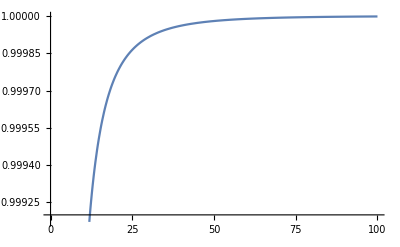

```mathematica
Pl201=ListInterpolation[Re[LDis1],{{0,100}}];
Plot[Pl201[y],{y,0,100}]
```

```mathematica
Pl21=ListInterpolation[Re[LDis22],{{0,80}}];
Pl22=ListInterpolation[Re[LDis32],{{80,160}}];
Pl23=ListInterpolation[Re[LDis42],{{160,240}}];
Pl24=ListInterpolation[Re[LDis5],{{0,100}}];Pl25=ListInterpolation[Re[LDis6],{{240,360}}];Pl26=ListInterpolation[Re[LDis7],{{360,450}}];
Pl27=ListInterpolation[Re[LDis8],{{450,600}}];
Pl28=ListInterpolation[Re[LDis9],{{600,700}}];
Pl29=ListInterpolation[Re[LDis10],{{700,795}}];
Pl210=ListInterpolation[Re[LDis11],{{795,850}}];
Pl211=ListInterpolation[Re[LDis12],{{850,900}}];
Pl212=ListInterpolation[Re[LDis13],{{900,950}}];Pl213=ListInterpolation[Re[LDis14],{{950,1000}}];
```

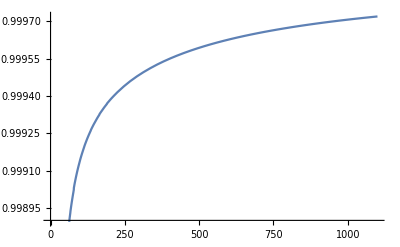

```mathematica
Fd[y_]:=Which[y<80,Pl21[y],80≤y≤160,Pl22[y],160≤y≤240,Pl23[y],240≤y≤360,Pl25[y],360≤y≤450,Pl26[y],450≤y≤600,Pl27[y],600≤y≤700,Pl28[y],700≤y≤795,Pl29[y],795≤y≤850,Pl210[y],850≤y≤900,Pl211[y],900≤y≤950,Pl212[y],950≤y≤1000,Pl213[y],y>1000,1-λ[y,200]^2];
Plot[Fd[y],{y,0,1100}]
```

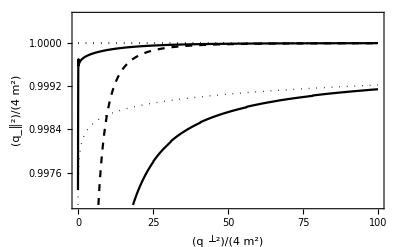

```mathematica
Fd2[y_]:=If[y<99,Pl24[y],1];
Plot[{Fd[y],Fd2[y],Pl201[y],1-λ[y,200]^2,1},{y,0,100},PlotRange->{0.997,1.0005},PlotStyle->{Black,Black,{Black,Dashed},{Black,Dotted,Thick},{Black,Dotted}},Frame->True,PlotRangePadding->0,FrameStyle->Thick,RotateLabel->False,FrameLabel->{(q_┴)^2/(4 m^2),(q_║)^2/(4 m^2)},LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin]]
```

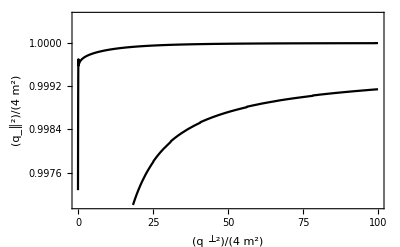

```mathematica
Plot[{Fd[y],Fd2[y]},{y,0,100},PlotRange->{0.997,1.0005},PlotStyle->{Black,Black,{Black,Dashed},{Black,Dotted,Thick},{Black,Dotted}},Frame->True,PlotRangePadding->0,FrameStyle->Thick,RotateLabel->False,FrameLabel->{(q_┴)^2/(4 m^2),(q_║)^2/(4 m^2)},LabelStyle->Directive[FontFamily->"Times",FontSize->18, Black,Thin]]
```

## Graph for W2-11 in plasma

```mathematica
F[x_]:=2Log[x]-1+1/x^2;
W1[x_]:=π/4(H[x,Fd[x],200])^2 Fd[x]/x^0.5 F[(x/Fd[x])^0.5](1+(α*200)/(2*π)*dH[x,Fd[x],200])^-1 UnitStep[x-Fd[x]];
W2[x_]:=π/4(H[x,Fd2[x],200])^2 Fd2[x]/x^0.5 F[(x/Fd2[x])^0.5](1+(α*200)/(2*π)*dH[x,Fd2[x],200])^-1 UnitStep[x-Fd2[x]];
```

```mathematica
FindRoot[0.94-Fd[y],{y,0}]
```

{y→2.42722}

```mathematica
W1[x_,y_]:=π/4(H[x,y,200])^2 y/x^0.5 F[(x/y)^0.5](1+(α*200)/(2*π)*dH[x,y,200])^-1 UnitStep[y-x];
```

```mathematica
W1[0.94,2.427218472509345]
```

0.0965492

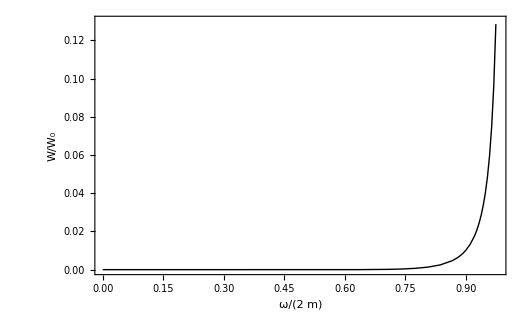

```mathematica
List1={{0,0},{0.4^0.5,0.000013901686385067311},{0.5^0.5,0.0001512750598997986},{0.55^0.5,0.00033802857235789484},{0.6^0.5,0.0006863717889706432},{0.65^0.5,0.0013219099646775098},{0.7^0.5,0.002480935687515901},{0.75^0.5,0.004636482117170117},{0.77^0.5,0.005976683977051727},{0.78^0.5,0.0067969876009640095},{0.79^0.5,0.007740641586813858},{0.8^0.5,0.008830720311548981},{0.81^0.5,0.010094730382586218},{0.83^0.5,0.0132919009316048},{0.85^0.5,0.017736353708698173},{0.86^0.5,0.02062287965404176},{0.87^0.5,0.02410867611922879},{0.88^0.5,0.028367606882443646},{0.89^0.5,0.03364083811272684},{0.9^0.5,0.04027413533874314},{0.91^0.5,0.048784243949877994},{0.92^0.5,0.059970556203540665},{0.93^0.5,0.07513701852645963},{0.94^0.5,0.09654921005119363},{0.95^0.5,0.12848472969240585},};
ListLinePlot[List1,PlotStyle->{{Thick,Black},{Black,Thick}},PlotRange->{{0,0.98},{0,0.13}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->16]
```

```mathematica
FindRoot[0.99935-Fd[y],{y,0}]
```

{y→178.227}

```mathematica
W1[0.99935,178.23592174373064]
```

80.2566

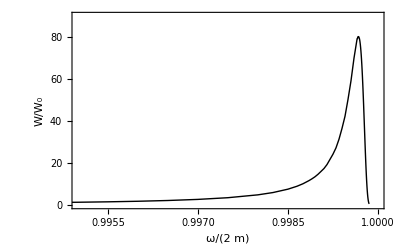

```mathematica
List2={{0.96^0.5,0.18001068495277134},{0.965^0.5,0.21912405093196682},{0.97^0.5,0.2739286187684039},{0.975^0.5,0.35525582289598},{0.98^0.5,0.4862817785118935},{0.985^0.5,0.7261509281290822},{0.99^0.5,1.2774129133017071},{0.991^0.5,1.4808948331138991},{0.992^0.5,1.7485880771915512},{0.993^0.5,2.1142084031366433},{0.994^0.5,2.63881309727627},{0.995^0.5,3.444247170865295},{0.996^0.5,4.809102650176511},{0.9965^0.5,5.9016411979948655},{0.997^0.5,7.516005465445315},{0.9973^0.5,8.900590339040914},{0.9975^0.5,10.09240396062303},{0.9977^0.5,11.589998840893314},{0.9978^0.5,12.454298671766916},{0.9979^0.5,13.418369221639267},{0.998^0.5,14.596706279674995},{0.9981^0.5,15.962479679095345},{0.9982^0.5,17.353911884755362},{0.9983^0.5,19.23638549914777},{0.9985^0.5,24.199079236006902},{0.9986^0.5,27.1961250315151},{0.9987^0.5,31.306831869321766},{0.9988^0.5,36.45723164094285},{0.9989^0.5,42.2393530456535},{0.999^0.5,50.26251531614401},{0.9991^0.5,59.18150200315062},{0.9992^0.5,69.97929671211607},{0.9993^0.5,78.88288802097831},{0.99931^0.5,79.42336498971353},{0.99932^0.5,79.33973045364888},{0.99933^0.5,80.14483214550549},{0.99934^0.5,80.20644375795011},{0.99935^0.5,80.25660976568689},{0.99936^0.5,80.1390080808658},{0.99938^0.5,79.34177281108917},{0.99939^0.5,78.62872040847259},{0.9994^0.5,77.70057451701297},{0.99941^0.5,76.54584953490453},{0.99942^0.5,75.15593492030251},{0.99943^0.5,73.52735522643809},{0.99944^0.5,71.62674011676359},{0.99945^0.5,69.48215439642225},{0.99946^0.5,67.08236997918507},{0.99947^0.5,64.43122356207599},{0.99948^0.5,61.53692174817916},{0.99949^0.5,58.412501450945875},{0.9995^0.5,55.07621412346619},{0.99952^0.5,47.86859960617545},{0.99955^0.5,36.24069849268416},{0.99957^0.5,28.46048498378945},{0.99958^0.5,24.713436177523448},{0.99959^0.5,21.130532171892416},{0.9996^0.5,17.760358405693438},{0.99961^0.5,14.646512771182007},{0.99962^0.5,11.825413778213242},{0.99963^0.5,9.324266811767986},{0.99964^0.5,7.159383686158433},{0.99965^0.5,5.33506119283922},{0.99966^0.5,3.843213065400858},{0.99967^0.5,2.6639056173516322},{0.99968^0.5,1.7668653823786664},{0.99969^0.5,1.1139112151741946},{0.9997^0.5,0.6621197459355951},{0.999705^0.5,0.49782500009010966}};
ListLinePlot[List2,PlotStyle->{{Thick,Black},{Black,Thick}},PlotRange->{{0.995,1},{0,90}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->16]
```